## Solution of the Schrödinger equation in momentum space for the linear potential, using the method described in Stadler, Biernat, Valverde, PHYSICAL REVIEW D 110, 114039 (2024). (C) 2024 Alfred Stadler

```mathematica
SetDirectory[NotebookDirectory[]]
```

Exact  solutions for l=0

```mathematica
Enx=Table[{k,-N[AiryAiZero[k]]},{k,1,20}]
```

{{1,2.33811},{2,4.08795},{3,5.52056},{4,6.78671},{5,7.94413},{6,9.02265},{7,10.0402},{8,11.0085},{9,11.936},{10,12.8288},{11,13.6915},{12,14.5278},{13,15.3408},{14,16.1327},{15,16.9056},{16,17.6613},{17,18.4011},{18,19.1264},{19,19.8381},{20,20.5373}}

Auxiliary  functions

```mathematica
Wl1[l1_,y_]:=Simplify[Sum[LegendreP[l1+1-mm,y]LegendreP[mm-1,y]/mm,{mm,1,l1+1}]]
```

```mathematica
DWl1[l1_,y_]:=D[Wl1[l1,yy],yy]/.yy->y//Simplify
```

```mathematica
DPl[l_,y_]:=D[LegendreP[l,yy],yy]/.yy->y//Simplify
```

Strength  parameter σ, reduced mass mr

```mathematica
σ=1.;mr=1/2;
```

Definition  of  quadrature  points

```mathematica
GaussianQuadWeights[n_,a_,b_]:=With[{ruledata=NIntegrate`GaussRuleData[n,MachinePrecision]},Transpose[{Rescale[ruledata[[1]],{0,1},{a,b}],Abs[b-a]ruledata[[2]]}]];
```

Selection of interpolations  points (algorithm described in Appendix)

```mathematica
s[i_,NL_,np_]:=If[OddQ[NL],Which[i<(NL+1)/2,0,i>np-(NL-1)/2,np-NL,True,i-(NL+1)/2],Which[i<(NL+2)/2,0,i>np-(NL-2)/2,np-NL,True,i-(NL+2)/2]]
```

Loops  over  l (angular momentum, from lmin to lmax), np (number of quadrature points), and NL (order of Lagrange interpolation)
nmax is the number of eigenstates to be printed out

```mathematica
lmin=0;lmax=5;nmax=20;
Do[Print["NL=",NL];Print["np=",np];{xp,xw}=Transpose[GaussianQuadWeights[np,-1.,1.]];
p0=1;
pw=p0*2 xw/(1-xp)^2;
pp=p0 (1+xp)/(1-xp);
y=Table[(pp[[i]]^2+pp[[j]]^2)/(2 pp[[i]] pp[[j]]),{i,1,np},{j,1,np}];
S1=Table[Sum[If[jj != i,pw[[jj]]2pp[[jj]]^2/(pp[[jj]]^2-pp[[i]]^2)^2,0],{jj,1,np}],{i,1,np}];
S2=Table[Sum[If[jj != i,pw[[jj]]/(pp[[jj]]^2-pp[[i]]^2),0],{jj,1,np}],{i,1,np}];
S3=Table[Sum[If[jj != i,pw[[jj]]/pp[[jj]] Log[((pp[[jj]]+pp[[i]])/(pp[[jj]]-pp[[i]]))^2],0],{jj,1,np}],{i,1,np}];
(*Define interpolating Lagrange polynomials and extract the coefficients*)
D1int=Table[0,{i,1,np},{j,1,np}];D2int=Table[0,{i,1,np},{j,1,np}];
Do[si=s[i,NL,np];Do[D1int[[i,j]]=
Sum[If[m != j,1/(pp[[j]]-pp[[m]])Product[
If[k !=j && k!= m ,(1-KroneckerDelta[k,i])(pp[[i]]-pp[[k]])/(pp[[j]]-pp[[k]]),1],{k,si+1,si+NL}],0],{m,si+1,si+NL}];D2int[[i,j]]=
Sum[If[m != j,1/(pp[[j]]-pp[[m]])Sum[If[l!=j && l!=m,1/(pp[[j]]-pp[[l]])Product[
If[k !=j && k!= m &&k != l,(pp[[i]]-pp[[k]])/(pp[[j]]-pp[[k]]),1],{k,si+1,si+NL}],0],{l,si+1,si+NL}],0],{m,si+1,si+NL}],{j,si+1,si+NL}],{i,1,np}];
(* Loop over angular momentum *)
Do[time0=SessionTime[];diag=Table[pp[[i]]^2/(2mr)+2σ/π(
S1[[i]]+ l(l+1)/(8pp[[i]])(π^2-S3[[i]]-pw[[i]]/pp[[i]])),{i,1,np}];
Mat=DiagonalMatrix[diag]+
2σ/π  (Table[pp[[i]] S2[[i]] D1int[[i,j]]-pw[[i]] 3/(4pp[[i]]) D1int[[i,j]]-pw[[i]]/4 D2int[[i,j]]-
pw[[j]]/(2pp[[i]]^2) DWl1[l-1,y[[i,j]]],{i,1,np},{j,1,np}]+
Table[If[j!=i,-pw[[j]]2 pp[[j]]^2/(pp[[j]]^2-pp[[i]]^2)^2LegendreP[l,y[[i,j]]]+pw[[j]]/(4pp[[i]]^2)DPl[l,y[[i,j]]]Log[((pp[[j]]+pp[[i]])/(pp[[j]]-pp[[i]]))^2],0],{i,1,np},{j,1,np}]);
{Eval,Evec}=Eigensystem[Mat];
En[l]=Take[Reverse[Chop[Eval]],nmax];Ev[l]=Take[Reverse[Chop[Evec]],nmax];
nrm=Table[Sum[pw[[i]]/(2π)^3 pp[[i]]^2 Ev[l][[n,i]]^2,{i,1,np}],{n,1,nmax}];
psi[l]=Table[If[Max[-Chop[Ev[l][[n]]]]>Max[Chop[Ev[l][[n]]]],-1,1]/Sqrt[nrm[[n]]]Chop[Ev[l][[n]]],{n,1,nmax}];
(*Save results*)
EntableLag[l,np,NL]=En[l];psitableLag[l,np,NL]=psi[l];
time1=SessionTime[];time=time1-time0;Print["Partial wave l="<>ToString[l]<>" complete. Elapsed time: " <>ToString[time]<>"  seconds."],{l,lmin,lmax}];
(* Print out results *)
resultstableLag[NL]=If[lmin==0,TableForm[Table[Join[{n},{InputForm[Enx[[n,2]]]},{InputForm[En[0][[n]]]},{NumberForm[En[0][[n]]-Enx[[n,2]],3]},Table[InputForm[En[l][[n]]],{l,1,lmax}]],{n,1,nmax}],TableHeadings->{None,Join[{"n","l=0 exact","l=0 numerical","l=0 difference"},Table["l="<>ToString[l],{l,1,lmax}]]}],TableForm[Table[Join[{n},Table[InputForm[En[l][[n]]],{l,lmin,lmax}]],{n,1,nmax}],TableHeadings->{None,Join[Table["l="<>ToString[l],{l,1,lmax}]]}]];
resgridLag[NL]=
If[lmin==0,
Grid[Join[{Join[{"n","l=0 exact","l=0 numerical","l=0 difference"},Table["l="<>ToString[l],{l,1,lmax}]]},Table[Join[{n},{FortranForm[Enx[[n,2]]]},{FortranForm[En[0][[n]]]},{NumberForm[En[0][[n]]-Enx[[n,2]],3]},Table[FortranForm[En[l][[n]]],{l,1,lmax}]],{n,1,nmax}]]],
Grid[Join[{Join[Table["l="<>ToString[l],{l,lmin,lmax}]]},Table[Join[Table[FortranForm[En[l][[n]]],{l,lmin,lmax}]],{n,1,nmax}]]]
];
Print[resgridLag[NL]];
(* Export results to file *)
Export["results-table-Lag-lmax"<>ToString[lmax]<>"-NL"<>ToString[NL]<>"-np="<>ToString[np]<>".txt",resgridLag[NL],"String"],{NL,{5,7,9}},{np,{50,100,200,400,600,800,1000}}
]
```

NL=5

np=50

Partial wave l=0 complete. Elapsed time: 0.067188  seconds.

Partial wave l=1 complete. Elapsed time: 0.066381  seconds.

Partial wave l=2 complete. Elapsed time: 0.248955  seconds.

Partial wave l=3 complete. Elapsed time: 0.625762  seconds.

Partial wave l=4 complete. Elapsed time: 1.102980  seconds.

Partial wave l=5 complete. Elapsed time: 1.697440  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338136658631928 | 0.0000292 | 3.3614264840889723 | 4.248461679063343 | 5.051240383655686 | 5.79461647114252 | 6.492819232648472
2 | 4.087949444130971 | 4.088381189600789 | 0.000432 | 4.8850105762850635 | 5.630358657621466 | 6.332837447212423 | 6.99999095108813 | 7.637566577445727
3 | 5.520559828095551 | 5.520509023507965 | -0.0000508 | 6.206860446830221 | 6.867231771533769 | 7.501983816741174 | 8.1134526272359 | 8.704095131515647
4 | 6.786708090071759 | 6.783098675253279 | -0.00361 | 7.399068077072054 | 7.999590423499643 | 8.583040625720642 | 9.149844051437984 | 9.700988145631758
5 | 7.944133587120853 | 7.930378021955142 | -0.0138 | 8.493976017431633 | 9.047057783524657 | 9.587518969005808 | 10.11498495123526 | 10.629765623324596
6 | 9.02265085334098 | 8.986887372963308 | -0.0358 | 9.506505103800372 | 10.017695636254627 | 10.51845033299561 | 11.008392995782156 | 11.487275171521274
7 | 10.040174341558085 | 9.962855347576093 | -0.0773 | 10.441427700005042 | 10.912315806176986 | 11.372087341823484 | 11.813636664861155 | 12.23047353088255
8 | 11.008524303733264 | 10.860067036271436 | -0.148 | 11.293893986869664 | 11.707138952597694 | 12.097104601973324 | 12.492759960919768 | 12.934881926874903
9 | 11.936015563236262 | 11.652049007569055 | -0.284 | 12.01563210985316 | 12.40404239429493 | 12.858328675774592 | 13.270033903803872 | 13.446643265084312
10 | 12.828776752865759 | 12.36443926998663 | -0.464 | 12.80974970669093 | 13.074954276842993 | 13.196376574068799 | 13.455978641168938 | 14.038412712633775
11 | 13.69148903521072 | 12.973632225056736 | -0.718 | 13.048760264319522 | 13.421549368691863 | 14.043975466122797 | 14.733862498222829 | 15.473240977771813
12 | 14.527829951775336 | 13.411921302609544 | -1.12 | 14.048682751797614 | 14.760284791513852 | 15.452536604195373 | 15.571636013106737 | 15.709768884574748
13 | 15.340755135977998 | 14.771273908821149 | -0.569 | 15.283175283587394 | 15.355255152697493 | 15.529569695674843 | 16.34799888846256 | 17.209827902276192
14 | 16.132685156945772 | 15.240916127219226 | -0.892 | 15.560133708396485 | 16.406724541719676 | 17.305050279618747 | 18.250600302017336 | 19.239757129504056
15 | 16.90563399742994 | 16.430758007844453 | -0.475 | 17.355764858602328 | 18.336338946513465 | 19.264338189433943 | 19.375021102946974 | 19.502037999160102
16 | 17.66130010569706 | 18.371198421897734 | 0.71 | 19.103766995771288 | 19.172753250492978 | 19.369113732610167 | 20.45115525896598 | 21.57984794265088
17 | 18.401132599207113 | 19.062334914655523 | 0.661 | 19.437343164172763 | 20.56132326809278 | 21.741224938497602 | 22.975040549065792 | 24.260755492450276
18 | 19.126380474246954 | 20.605806668910496 | 1.48 | 21.825592255564384 | 23.108535004633076 | 24.45380210973096 | 25.23227604515925 | 25.346217673460576
19 | 19.8381298917215 | 23.16198165033066 | 3.32 | 24.55373410983465 | 25.04878623101995 | 25.132264629186164 | 25.86005169789768 | 27.325678226818866
20 | 20.537332907677566 | 24.94641266550336 | 4.41 | 24.985209013931932 | 26.01687651136762 | 27.5515583710178 | 29.156991933553 | 30.83187250067705

NL=5

np=100

Partial wave l=0 complete. Elapsed time: 0.245463  seconds.

Partial wave l=1 complete. Elapsed time: 0.256089  seconds.

Partial wave l=2 complete. Elapsed time: 1.000884  seconds.

Partial wave l=3 complete. Elapsed time: 2.534733  seconds.

Partial wave l=4 complete. Elapsed time: 4.699435  seconds.

Partial wave l=5 complete. Elapsed time: 6.885356  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381083586824922 | 9.48×10^-7 | 3.361264331693152 | 4.24820117289319 | 5.050947791476121 | 5.794431644122319 | 6.492982095548103
2 | 4.087949444130971 | 4.087963775893229 | 0.0000143 | 4.884485146715971 | 5.629774998871867 | 6.332229946465137 | 6.999432521051752 | 7.63719734632984
3 | 5.520559828095551 | 5.520560299469179 | 4.71×10^-7 | 6.2076297618105905 | 6.868921842079827 | 7.5047496705042445 | 8.117460475578108 | 8.709551378446179
4 | 6.786708090071759 | 6.786592838499662 | -0.000115 | 7.40549485541788 | 8.009509823291133 | 8.596943999787417 | 9.168219774873942 | 9.724355363709865
5 | 7.944133587120853 | 7.943670124611788 | -0.000463 | 8.514569694173646 | 9.076164869142543 | 9.626295867544798 | 10.164606585018676 | 10.691398500585022
6 | 9.02265085334098 | 9.02139568109268 | -0.00126 | 9.55587993673151 | 10.084248018924917 | 10.604336277729457 | 11.115467547060572 | 11.61757825626532
7 | 10.040174341558085 | 10.037364677695269 | -0.00281 | 10.542753480738538 | 11.043971550711243 | 11.538993478148734 | 12.027020316375864 | 12.507798350276133
8 | 11.008524303733264 | 11.002937842466531 | -0.00559 | 11.484123438020259 | 11.962366827457243 | 12.435815777101094 | 12.903640597826216 | 13.365488942905746
9 | 11.936015563236262 | 11.925795228502096 | -0.0102 | 12.386141294097108 | 12.844321208450195 | 13.298653016209316 | 13.74831797197787 | 14.192914199436503
10 | 12.828776752865759 | 12.811216575725803 | -0.0176 | 13.253038393955874 | 13.693158776557063 | 14.130049919548311 | 14.56292142642182 | 14.991347673139119
11 | 13.69148903521072 | 13.662775766723918 | -0.0287 | 14.087610034704104 | 14.510972630459072 | 14.931469244227767 | 15.348341900704757 | 15.761152611706725
12 | 14.527829951775336 | 14.482730856162602 | -0.0451 | 14.891487333545829 | 15.298804597474206 | 15.70339895774658 | 16.104539797360932 | 16.501776435131667
13 | 15.340755135977998 | 15.272235049375317 | -0.0685 | 15.665271568189205 | 16.05671331778441 | 16.44535974350234 | 16.83048841655509 | 17.21161575796347
14 | 16.132685156945772 | 16.031422130837566 | -0.101 | 16.408555886158148 | 16.783725160876884 | 17.15577183884696 | 17.523977715917706 | 17.887906051324148
15 | 16.90563399742994 | 16.75936596924276 | -0.146 | 17.11980038710253 | 17.477664680780325 | 17.831919437206853 | 18.18179843130125 | 18.525917569220898
16 | 17.66130010569706 | 17.453929440406885 | -0.207 | 17.796332923675934 | 18.135219727154002 | 18.468214797787724 | 18.792056007800674 | 19.106913183836568
17 | 18.401132599207113 | 18.111731649712375 | -0.289 | 18.43198758124986 | 18.743415668715052 | 19.047851769328418 | 19.358205422464305 | 19.683667270446335
18 | 19.126380474246954 | 18.719548362337758 | -0.407 | 19.012253997618714 | 19.314867481657057 | 19.628096031857783 | 19.8642558387798 | 20.010924686651283
19 | 19.8381298917215 | 19.294112245097164 | -0.544 | 19.590706224978195 | 19.786099729445514 | 19.918416675388553 | 20.165890681484008 | 20.56473999946888
20 | 20.537332907677566 | 19.74855973593061 | -0.789 | 19.868844410992498 | 20.139007131509473 | 20.5506413491531 | 21.01937329981301 | 21.276609410140036

NL=5

np=200

Partial wave l=0 complete. Elapsed time: 0.961849  seconds.

Partial wave l=1 complete. Elapsed time: 1.024427  seconds.

Partial wave l=2 complete. Elapsed time: 4.010133  seconds.

Partial wave l=3 complete. Elapsed time: 10.136507  seconds.

Partial wave l=4 complete. Elapsed time: 17.986302  seconds.

Partial wave l=5 complete. Elapsed time: 27.839491  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338107440555187 | 3.01×10^-8 | 3.361255365420102 | 4.248184087413361 | 5.050927816610263 | 5.794423356406416 | 6.493012690772995
2 | 4.087949444130971 | 4.087949901919106 | 4.58×10^-7 | 4.8844547204190905 | 5.629716089326467 | 6.3321303465965775 | 6.9992844074095855 | 7.637000720072027
3 | 5.520559828095551 | 5.520559862435771 | 3.43×10^-8 | 6.207627136173129 | 6.8688954351300175 | 7.504673124635783 | 8.117307609163753 | 8.709299687706798
4 | 6.786708090071759 | 6.786704451405569 | -3.64×10^-6 | 7.405665871196762 | 8.009715433712177 | 8.597151019232019 | 9.168391858233061 | 9.724456521691494
5 | 7.944133587120853 | 7.944118709756992 | -0.0000149 | 8.515221349762337 | 9.077002928171622 | 9.627292671710434 | 10.165728936382843 | 10.692611157374499
6 | 9.02265085334098 | 9.022609986988325 | -0.0000409 | 9.557570577315273 | 10.086423536510285 | 10.606992642486961 | 11.118593834401025 | 11.621160090906885
7 | 10.040174341558085 | 10.04008152067054 | -0.0000928 | 10.54641173336889 | 11.048628327441492 | 11.544692832558253 | 12.033799147623792 | 12.515689783992126
8 | 11.008524303733264 | 11.008336910262942 | -0.000187 | 11.491199199990083 | 11.97125527196661 | 12.446640517157789 | 12.916519081022114 | 13.380535810956491
9 | 11.936015563236262 | 11.935667273791772 | -0.000348 | 12.398791810501526 | 12.860003111269435 | 13.317608974281242 | 13.77078710020252 | 14.219135550980248
10 | 12.828776752865759 | 12.828168667219058 | -0.000608 | 13.27435364855034 | 13.719254276487518 | 14.161336691289437 | 14.59981200260893 | 15.03426008748815
11 | 13.69148903521072 | 13.69047881282812 | -0.00101 | 14.121884364928725 | 14.552458509943039 | 14.980808465394075 | 15.406186957364467 | 15.828171940890225
12 | 14.527829951775336 | 14.526218798016098 | -0.00161 | 14.94454974702057 | 15.362380527287131 | 15.778442523221772 | 16.19203239671541 | 16.602735387393167
13 | 15.340755135977998 | 15.338272504325271 | -0.00248 | 15.74489728562768 | 16.15126608284672 | 16.556219127877654 | 16.959096369916438 | 17.3594954052677
14 | 16.132685156945772 | 16.12897104560555 | -0.00371 | 16.525001931322826 | 16.920956801223074 | 17.31577130960413 | 17.708826599147738 | 18.099735229067303
15 | 16.90563399742994 | 16.90021873114016 | -0.00542 | 17.28656758274435 | 17.67297159328697 | 18.05845024406962 | 18.44242313807583 | 18.824518916358148
16 | 17.66130010569706 | 17.653581491007646 | -0.00772 | 18.030999443752627 | 18.408565547502747 | 18.785373149754957 | 19.16087736788679 | 19.53472314149119
17 | 18.401132599207113 | 18.390350331382358 | -0.0108 | 18.7594565819663 | 19.128773183314294 | 19.49745879595594 | 19.865001113841213 | 20.23106104296433
18 | 19.126380474246954 | 19.111587643976257 | -0.0148 | 19.47289062840281 | 19.834440539977667 | 20.19545398782657 | 20.555448419144685 | 20.914100038892368
19 | 19.8381298917215 | 19.81816139363858 | -0.02 | 20.1720744962356 | 20.526249065497723 | 20.879953285619163 | 21.232731689483494 | 21.584274904921486
20 | 20.537332907677566 | 20.510770478659072 | -0.0266 | 20.857623692415828 | 21.20473329015703 | 21.551413474124445 | 21.897233353956075 | 22.241896965147156

NL=5

np=400

Partial wave l=0 complete. Elapsed time: 3.882567  seconds.

Partial wave l=1 complete. Elapsed time: 4.140161  seconds.

Partial wave l=2 complete. Elapsed time: 16.128559  seconds.

Partial wave l=3 complete. Elapsed time: 40.824894  seconds.

Partial wave l=4 complete. Elapsed time: 71.946786  seconds.

Partial wave l=5 complete. Elapsed time: 111.116025  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074114068525 | 9.47×10^-10 | 3.361254616196343 | 4.248182469165301 | 5.050925889083682 | 5.7944228536358064 | 6.493016930238317
2 | 4.087949444130971 | 4.087949458560966 | 1.44×10^-8 | 4.884452162337382 | 5.629709321629289 | 6.332117268450246 | 6.999263428024983 | 7.63697118307045
3 | 5.520559828095551 | 5.520559829333533 | 1.24×10^-9 | 6.207623868705494 | 6.868884533667052 | 7.504649546047499 | 8.117266204990296 | 8.709235633739294
4 | 6.786708090071759 | 6.786707975728803 | -1.14×10^-7 | 7.405666187351099 | 8.009705673838852 | 8.597123082249931 | 9.16833697169977 | 9.724365674603558
5 | 7.944133587120853 | 7.9441331175868015 | -4.7×10^-7 | 8.515234969570638 | 9.077006479391963 | 9.62727510419985 | 10.165678014621855 | 10.692513897873795
6 | 9.02265085334098 | 9.022649558769071 | -1.29×10^-6 | 9.557615941397447 | 10.086463313858879 | 10.607013207974012 | 11.11857992385854 | 11.621095242826001
7 | 10.040174341558085 | 10.04017138956903 | -2.95×10^-6 | 10.546520538835795 | 11.048743205620434 | 11.54479826461909 | 12.033877589516559 | 12.51572211281196
8 | 11.008524303733264 | 11.008518318566944 | -5.99×10^-6 | 11.491422402473628 | 11.97150687292244 | 12.44690413059633 | 12.916775983779937 | 13.380765393740308
9 | 11.936015563236262 | 11.936004387662798 | -0.0000112 | 12.39920728434951 | 12.860484345906844 | 13.318140123052858 | 13.771349746584125 | 14.219709164141968
10 | 12.828776752865759 | 12.828757143777905 | -0.0000196 | 13.275075686536635 | 13.720099809576729 | 14.162292228920048 | 14.600861334445046 | 15.035384742985197
11 | 13.69148903521072 | 13.691456284170892 | -0.0000328 | 14.1230751726633 | 14.553857292802656 | 14.982406342207728 | 15.407972261875928 | 15.830130685103537
12 | 14.527829951775336 | 14.527777421730777 | -0.0000525 | 14.94643306989779 | 15.36459052569698 | 15.78097763806614 | 16.194888303762017 | 16.605905465117534
13 | 15.340755135977998 | 15.340673705707065 | -0.0000814 | 15.747774286045905 | 16.1546313107129 | 16.560081538995597 | 16.963462260315428 | 17.36436888586809
14 | 16.132685156945772 | 16.132562564923376 | -0.000123 | 16.529269422823262 | 16.92592676235502 | 17.321466904727927 | 17.715268524403026 | 18.106942197731208
15 | 16.90563399742994 | 16.905454077204563 | -0.00018 | 17.29273872179141 | 17.680123233265277 | 18.066623975603058 | 18.451658364136293 | 18.834853353157232
16 | 17.66130010569706 | 17.661041905121003 | -0.000258 | 18.039726986854884 | 18.418627830648056 | 18.796834960895616 | 19.173801683300834 | 19.549171648217644
17 | 18.401132599207113 | 18.400769376311036 | -0.000363 | 18.771558835229307 | 19.14265443779146 | 19.513212401032554 | 19.882719089701737 | 20.250834635905193
18 | 19.126380474246954 | 19.125878562890147 | -0.000502 | 19.489380254926676 | 19.853258762397758 | 20.216728729722593 | 20.579306882903968 | 20.94066931160891
19 | 19.8381298917215 | 19.837447430609707 | -0.000682 | 20.194190406192828 | 20.551365448998794 | 20.908239380338678 | 21.264356776255802 | 21.619408987425647
20 | 20.537332907677566 | 20.536418426725092 | -0.000914 | 20.886866328700286 | 21.237789344296786 | 21.588501075467587 | 21.93857164283136 | 22.287706874417797

NL=5

np=600

Partial wave l=0 complete. Elapsed time: 8.730226  seconds.

Partial wave l=1 complete. Elapsed time: 9.319337  seconds.

Partial wave l=2 complete. Elapsed time: 36.634096  seconds.

Partial wave l=3 complete. Elapsed time: 91.180549  seconds.

Partial wave l=4 complete. Elapsed time: 162.583392  seconds.

Partial wave l=5 complete. Elapsed time: 249.253611  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074105848136 | 1.25×10^-10 | 3.361254549942373 | 4.248182319076534 | 5.050925709240074 | 5.794422816371358 | 6.49301736794871
2 | 4.087949444130971 | 4.087949446035852 | 1.9×10^-9 | 4.884451936144302 | 5.6297086559227125 | 6.332115937333583 | 6.9992612557554335 | 7.636968087158285
3 | 5.520559828095551 | 5.520559828262413 | 1.67×10^-10 | 6.207623469360698 | 6.868883250012214 | 7.504646825310157 | 8.117261479167675 | 8.709228366657548
4 | 6.786708090071759 | 6.786708074984418 | -1.51×10^-8 | 7.405665697038289 | 8.009703804190986 | 8.597118912747172 | 9.168329503875272 | 9.72435388118216
5 | 7.944133587120853 | 7.944133525118163 | -6.2×10^-8 | 8.515234627517325 | 9.077004259243392 | 9.62726968447905 | 10.16566793703115 | 10.692497613619073
6 | 9.02265085334098 | 9.02265068227275 | -1.71×10^-7 | 9.55761623967335 | 10.0864612936867 | 10.607007123993716 | 11.118567835120523 | 11.621075060157194
7 | 10.040174341558085 | 10.04017395118643 | -3.9×10^-7 | 10.546522356157734 | 11.048742404996759 | 11.544792662933995 | 12.033864753579008 | 12.515699405193233
8 | 11.008524303733264 | 11.008523511616485 | -7.92×10^-7 | 11.4914271842735 | 11.97150898521097 | 12.446900951566255 | 12.916764588254894 | 13.38074260200407
9 | 11.936015563236262 | 11.936014082888384 | -1.48×10^-6 | 12.399217276249166 | 12.860492000436457 | 13.318142390784757 | 13.77134322735331 | 14.219690152353403
10 | 12.828776752865759 | 12.828774152914235 | -2.6×10^-6 | 13.275094229054414 | 13.72011689894825 | 14.162304416320094 | 14.600864772122486 | 15.03537523329329
11 | 13.69148903521072 | 13.691484688299973 | -4.35×10^-6 | 14.123107064467973 | 14.553889372548102 | 14.982434803258114 | 15.407992857966425 | 15.830138776597583
12 | 14.527829951775336 | 14.527822971929924 | -6.98×10^-6 | 14.946485007051782 | 15.36464529356211 | 15.78103113382107 | 16.1949359447668 | 16.60594224080804
13 | 15.340755135977998 | 15.340744303156857 | -0.0000108 | 15.747855384241308 | 16.154719172461462 | 16.560171843216906 | 16.96355017556612 | 17.36444911639469
14 | 16.132685156945772 | 16.132668827497998 | -0.0000163 | 16.529391829512704 | 16.926061490803765 | 17.321609518440667 | 17.71541404280841 | 18.107085149498964
15 | 16.90563399742994 | 16.90560999919572 | -0.000024 | 17.292918324692163 | 17.680322726873623 | 18.066838926520674 | 18.45188377464172 | 18.835083705933204
16 | 17.66130010569706 | 17.661265616485487 | -0.0000345 | 18.039984225036495 | 18.418914977668738 | 18.79714773339225 | 19.1741352102878 | 19.549520524334454
17 | 18.401132599207113 | 18.401084007408674 | -0.0000486 | 18.77191961856327 | 19.143058091586408 | 19.51365495794469 | 19.88319598339953 | 20.251340749237784
18 | 19.126380474246954 | 19.126313220360462 | -0.0000673 | 19.489876997350922 | 19.85381483314732 | 20.217340673918144 | 20.57997063104338 | 20.94138024100936
19 | 19.8381298917215 | 19.838038289585946 | -0.0000916 | 20.194863177789575 | 20.552118116625255 | 20.909069217197835 | 21.265260441030975 | 21.620382576967053
20 | 20.537332907677566 | 20.53720994424319 | -0.000123 | 20.88776413125211 | 21.23879239705966 | 21.589607628654683 | 21.93977932745339 | 22.289012765914507

NL=5

np=800

Partial wave l=0 complete. Elapsed time: 15.540851  seconds.

Partial wave l=1 complete. Elapsed time: 16.625505  seconds.

Partial wave l=2 complete. Elapsed time: 65.083604  seconds.

Partial wave l=3 complete. Elapsed time: 162.426052  seconds.

Partial wave l=4 complete. Elapsed time: 290.241059  seconds.

Partial wave l=5 complete. Elapsed time: 448.039447  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338107410490693 | 3.09×10^-11 | 3.3612545342574025 | 4.248182283147798 | 5.050925666129944 | 5.794422808191137 | 6.493017475036187
2 | 4.087949444130971 | 4.087949444583076 | 4.52×10^-10 | 4.884451882602989 | 5.629708494529001 | 6.332115612333484 | 6.999260723742054 | 7.636967326679269
3 | 5.520559828095551 | 5.5205598281350845 | 3.95×10^-11 | 6.207623368599059 | 6.868882928050364 | 7.504646145305973 | 8.117260301478705 | 8.709226554020809
4 | 6.786708090071759 | 6.786708086489368 | -3.58×10^-9 | 7.405665551608952 | 8.009703304469268 | 8.597117829091065 | 9.168327589119368 | 9.724350873255446
5 | 7.944133587120853 | 7.944133572388869 | -1.47×10^-8 | 8.515234458555824 | 9.077003589254065 | 9.627268181167787 | 10.165665234384987 | 10.692493317272282
6 | 9.02265085334098 | 9.022650812683706 | -4.07×10^-8 | 9.55761609799087 | 10.086460498309638 | 10.607005230177512 | 11.11856435044222 | 11.621069449905365
7 | 10.040174341558085 | 10.040174248755651 | -9.28×10^-8 | 10.546522337815455 | 11.048741584326972 | 11.544790475753885 | 12.033860572747674 | 12.515692547529563
8 | 11.008524303733264 | 11.00852411537224 | -1.88×10^-7 | 11.491427451677293 | 11.971508318509668 | 12.446898660606275 | 12.916759906815264 | 13.38073469022249
9 | 11.936015563236262 | 11.936015211109492 | -3.52×10^-7 | 12.399218085609736 | 12.860491776960663 | 13.318140314719159 | 13.771338387528957 | 14.219681551414066
10 | 12.828776752865759 | 12.828776134213596 | -6.19×10^-7 | 13.275095965185225 | 13.720117556642439 | 14.162303042076012 | 14.60086030998479 | 15.035366528426154
11 | 13.69148903521072 | 13.691488000497902 | -1.03×10^-6 | 14.123110283863143 | 14.553891545512318 | 14.982434843338222 | 15.407989561630396 | 15.830130832065185
12 | 14.527829951775336 | 14.527828289682777 | -1.66×10^-6 | 14.946490490212039 | 15.364649869259535 | 15.781033583224609 | 16.194934921421385 | 16.60593627567382
13 | 15.340755135977998 | 15.340752555298709 | -2.58×10^-6 | 15.747864198190825 | 16.154727359609893 | 16.56017805811361 | 16.963552930060942 | 17.364446790776114
14 | 16.132685156945772 | 16.132681265059087 | -3.89×10^-6 | 16.52940540147704 | 16.926074898902357 | 17.321621294390344 | 17.715422569147787 | 18.10708866325121
15 | 16.90563399742994 | 16.90562827503618 | -5.72×10^-6 | 17.29293852786285 | 17.680343458293 | 18.066858607653007 | 18.45190066312955 | 18.83509590772058
16 | 17.66130010569706 | 17.661291877490925 | -8.23×10^-6 | 18.040013477356432 | 18.41894573322284 | 18.797178313130605 | 19.174163765566476 | 19.549545039713443
17 | 18.401132599207113 | 18.401121000156834 | -0.0000116 | 18.771960995451323 | 19.143102290496195 | 19.51370021748746 | 19.883240359962016 | 20.25138212495995
18 | 19.126380474246954 | 19.126364411172663 | -0.0000161 | 19.489934359243698 | 19.853876748263207 | 20.217405314177512 | 20.58003598436407 | 20.94144410202969
19 | 19.8381298917215 | 19.838107999839117 | -0.0000219 | 20.194941313381392 | 20.552203025770883 | 20.909159031123238 | 21.265353095514964 | 21.62047580478541
20 | 20.537332907677566 | 20.537303501786983 | -0.0000294 | 20.88786891726064 | 21.23890675132735 | 21.58972966450408 | 21.93990696225776 | 22.28914369994555

NL=5

np=1000

Partial wave l=0 complete. Elapsed time: 24.159820  seconds.

Partial wave l=1 complete. Elapsed time: 25.920155  seconds.

Partial wave l=2 complete. Elapsed time: 101.394398  seconds.

Partial wave l=3 complete. Elapsed time: 259.246923  seconds.

Partial wave l=4 complete. Elapsed time: 457.012925  seconds.

Partial wave l=5 complete. Elapsed time: 713.369256  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074104672734 | 7.51×10^-12 | 3.361254528731092 | 4.248182270434725 | 5.050925650189408 | 5.794422805307164 | 6.493017513471443
2 | 4.087949444130971 | 4.0879494442789355 | 1.48×10^-10 | 4.8844518637368255 | 5.62970843713385 | 6.33211549645013 | 6.999260533455541 | 7.636967054997752
3 | 5.520559828095551 | 5.520559828113302 | 1.78×10^-11 | 6.207623332237513 | 6.868882812108645 | 7.504645900476435 | 8.117259876909012 | 8.709225903533014
4 | 6.786708090071759 | 6.786708088892988 | -1.18×10^-9 | 7.405665496330213 | 8.009703120525831 | 8.597117433879497 | 9.168326891887773 | 9.724349785025268
5 | 7.944133587120853 | 7.9441335822902035 | -4.83×10^-9 | 8.51523438692537 | 9.077003333302374 | 9.627267620821158 | 10.165664236411358 | 10.692491743941012
6 | 9.02265085334098 | 9.02265084000595 | -1.33×10^-8 | 9.557616018867117 | 10.086460174387652 | 10.607004500403002 | 11.11856303535787 | 11.621067359380621
7 | 10.040174341558085 | 10.040174311118946 | -3.04×10^-8 | 10.54652226959448 | 11.048741208188895 | 11.544789586349285 | 12.03385894088014 | 12.515689928554583
8 | 11.008524303733264 | 11.00852424194279 | -6.18×10^-8 | 11.491427426724425 | 11.97150792264255 | 12.446897641023778 | 12.916757981597122 | 13.380731558569943
9 | 11.936015563236262 | 11.936015447707396 | -1.16×10^-7 | 12.399218156031647 | 12.860491417055194 | 13.318139221759601 | 13.771336224059981 | 14.219677956984972
10 | 12.828776752865759 | 12.828776549861649 | -2.03×10^-7 | 13.275096210165561 | 13.720117319743768 | 14.162301968418962 | 14.600858005129613 | 15.035362567974053
11 | 13.69148903521072 | 13.691488695623928 | -3.4×10^-7 | 14.123110818757501 | 14.553891560041079 | 14.982433928646515 | 15.407987264921607 | 15.83012666406208
12 | 14.527829951775336 | 14.527829406188106 | -5.46×10^-7 | 14.94649147760749 | 15.364650317115464 | 15.781033027508174 | 16.19493284956155 | 16.605932133711857
13 | 15.340755135977998 | 15.340754288695251 | -8.47×10^-7 | 15.747865861157898 | 16.154728490566338 | 16.560178137079042 | 16.96355138403137 | 17.364443001433408
14 | 16.132685156945772 | 16.13268387890423 | -1.28×10^-6 | 16.529408039213525 | 16.926077047510095 | 17.321622377852886 | 17.71542195377143 | 18.10708566633542
15 | 16.90563399742994 | 16.90563211785461 | -1.88×10^-6 | 17.292942533937502 | 17.680347063481484 | 18.066861180217753 | 18.451901509168245 | 18.835094282475556
16 | 17.66130010569706 | 17.661297402414473 | -2.7×10^-6 | 18.040019360784466 | 18.418951360860135 | 18.797182998253277 | 19.174166755937637 | 19.549545531220716
17 | 18.401132599207113 | 18.40112878750279 | -3.81×10^-6 | 18.771969404793094 | 19.143110659059822 | 19.513707805435548 | 19.883246358745716 | 20.251385672949713
18 | 19.126380474246954 | 19.126375194136752 | -5.28×10^-6 | 19.48994610995704 | 19.8538887578758 | 20.21741679119616 | 20.580046068726322 | 20.941451878509582
19 | 19.8381298917215 | 19.838122693556794 | -7.2×10^-6 | 20.19495741861537 | 20.55221979079127 | 20.90917561558531 | 21.265368592061876 | 21.62048925144168
20 | 20.537332907677566 | 20.537323235942512 | -9.67×10^-6 | 20.887890622320423 | 21.238929636700245 | 21.589752845595733 | 21.939929487889813 | 22.289164561919765

NL=7

np=50

Partial wave l=0 complete. Elapsed time: 0.063381  seconds.

Partial wave l=1 complete. Elapsed time: 0.066725  seconds.

Partial wave l=2 complete. Elapsed time: 0.252868  seconds.

Partial wave l=3 complete. Elapsed time: 0.632783  seconds.

Partial wave l=4 complete. Elapsed time: 1.123458  seconds.

Partial wave l=5 complete. Elapsed time: 1.725807  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338103325386625 | -4.09×10^-6 | 3.3612938671158603 | 4.248299147427378 | 5.051097228124551 | 5.794538659458041 | 6.492850158106039
2 | 4.087949444130971 | 4.087984565551419 | 0.0000351 | 4.884784852690416 | 5.630560902418389 | 6.333679604743724 | 7.001664815798654 | 7.64024405015915
3 | 5.520559828095551 | 5.521181687483937 | 0.000622 | 6.2090102888680025 | 6.871358170395208 | 7.508487534962805 | 8.122669070522367 | 8.716297950601028
4 | 6.786708090071759 | 6.788474145334503 | 0.00177 | 7.408227416694706 | 8.013134853583123 | 8.601390816640114 | 9.173288248228069 | 9.729692849462657
5 | 7.944133587120853 | 7.945828420726358 | 0.00169 | 8.515977889438163 | 9.076008607625939 | 9.623540715276825 | 10.157984438761103 | 10.679450440336225
6 | 9.02265085334098 | 9.018138399869926 | -0.00451 | 9.546600932054904 | 10.066397354981452 | 10.575124603866895 | 11.07204293313978 | 11.556346705276402
7 | 10.040174341558085 | 10.01387859565487 | -0.0263 | 10.501836535691547 | 10.980525904792373 | 11.445310223078405 | 11.886717803472255 | 12.296916271739546
8 | 11.008524303733264 | 10.93006684271763 | -0.0785 | 11.368943334997317 | 11.780129948350831 | 12.161857630483832 | 12.551759867427005 | 12.997388827010772
9 | 11.936015563236262 | 11.725153706672671 | -0.211 | 12.08103172024091 | 12.467509733936774 | 12.93185995124446 | 13.270216518232463 | 13.41842826936777
10 | 12.828776752865759 | 12.431395726471024 | -0.397 | 12.888782301399594 | 13.057319519520883 | 13.161019744007696 | 13.497085819486799 | 14.110576645979595
11 | 13.69148903521072 | 12.95194381552083 | -0.74 | 13.01147389481622 | 13.485240848826267 | 14.126832572045027 | 14.827406076984444 | 15.575142673431937
12 | 14.527829951775336 | 13.481608285715469 | -1.05 | 14.13756473026812 | 14.86159650906893 | 15.433404520493644 | 15.552646249205981 | 15.690931619820091
13 | 15.340755135977998 | 14.876151291410348 | -0.465 | 15.263813444494565 | 15.335992501734259 | 15.641094079102542 | 16.468432451646237 | 17.338192442039844
14 | 16.132685156945772 | 15.221489905691886 | -0.911 | 15.677699225036395 | 16.535649964410403 | 17.44422756919088 | 18.39909633351159 | 19.39672900166898
15 | 16.90563399742994 | 16.563665568818575 | -0.342 | 17.501875990473504 | 18.49467302884982 | 19.242815988716686 | 19.35361143961038 | 19.480750526905098
16 | 17.66130010569706 | 18.534194708456035 | 0.873 | 19.08207246902579 | 19.15113392846343 | 19.538635364515503 | 20.630914125205475 | 21.768936573169224
17 | 18.401132599207113 | 19.04059466009262 | 0.639 | 19.615041112811404 | 20.752685499141243 | 21.94507033315069 | 23.19027240045569 | 24.486313471877573
18 | 19.126380474246954 | 20.802719251664808 | 1.68 | 22.03920484234567 | 23.337595015812195 | 24.696857033687454 | 25.207797974658295 | 25.321832741570486
19 | 19.8381298917215 | 23.397721707274936 | 3.56 | 24.808571613763483 | 25.024144532229915 | 25.107699519936922 | 26.115770368501927 | 27.592777740532064
20 | 20.537332907677566 | 24.921671456500004 | 4.38 | 24.96050640159975 | 26.28921290495149 | 27.8395448406528 | 29.458973277849495 | 31.14626964370239

NL=7

np=100

Partial wave l=0 complete. Elapsed time: 0.246104  seconds.

Partial wave l=1 complete. Elapsed time: 0.261741  seconds.

Partial wave l=2 complete. Elapsed time: 1.012112  seconds.

Partial wave l=3 complete. Elapsed time: 2.665490  seconds.

Partial wave l=4 complete. Elapsed time: 4.513312  seconds.

Partial wave l=5 complete. Elapsed time: 7.014432  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338107375857867 | -3.46×10^-8 | 3.361260113707438 | 4.2481954169447365 | 5.050941711642205 | 5.7944264620687065 | 6.492979074366495
2 | 4.087949444130971 | 4.087949724828459 | 2.81×10^-7 | 4.88447263573251 | 5.629771132956328 | 6.332241317620967 | 6.999465934506024 | 7.63725982514962
3 | 5.520559828095551 | 5.520565350749564 | 5.52×10^-6 | 6.207671862202393 | 6.8690199149043005 | 7.5049223979067445 | 8.117727090483779 | 8.709931586649537
4 | 6.786708090071759 | 6.786726103795536 | 0.000018 | 7.405751669805226 | 8.009928662466818 | 8.597563343061188 | 9.169078932640277 | 9.725494275027996
5 | 7.944133587120853 | 7.944159755982753 | 0.0000262 | 8.515343526051604 | 9.077289267836916 | 9.627837187488776 | 10.166631994583303 | 10.69397562251505
6 | 9.02265085334098 | 9.022636317628034 | -0.0000145 | 9.557663814472221 | 10.086677646559716 | 10.607513557364744 | 11.119494615672828 | 11.622556967115589
7 | 10.040174341558085 | 10.03996594440748 | -0.000208 | 10.546278998129266 | 11.048567210006663 | 11.544803153109592 | 12.034186768924387 | 12.516462591313473
8 | 11.008524303733264 | 11.007770286615463 | -0.000754 | 11.4904038612966 | 11.970289977295726 | 12.445571992436108 | 12.915416893772402 | 13.379468342217034
9 | 11.936015563236262 | 11.934029385461745 | -0.00199 | 12.396506093065483 | 12.857063395578749 | 13.314011572875888 | 13.766525543792602 | 14.214196544959112
10 | 12.828776752865759 | 12.82435206089068 | -0.00442 | 13.269156602877052 | 13.712559144294875 | 14.153019988058487 | 14.589738851385167 | 15.022280002154377
11 | 13.69148903521072 | 13.682658475409376 | -0.00883 | 14.111501571275028 | 14.539223711569855 | 14.964414239036026 | 15.3863017184957 | 15.804435089311019
12 | 14.527829951775336 | 14.511558614308328 | -0.0163 | 14.925523749954676 | 15.33844919989877 | 15.749030860773502 | 16.156521807859832 | 16.560456549770308
13 | 15.340755135977998 | 15.31255447849213 | -0.0282 | 15.712170561690124 | 16.110638422361617 | 16.506734833773827 | 16.899722605200736 | 17.28911098178184
14 | 16.132685156945772 | 16.086122748884108 | -0.0466 | 16.471377897149907 | 16.85516778204292 | 17.23631994572713 | 17.61410492806778 | 17.98803566751348
15 | 16.90563399742994 | 16.831687242378955 | -0.0739 | 17.20198051536238 | 17.57026759096773 | 17.93543139138134 | 18.29659964044144 | 18.65259671968116
16 | 17.66130010569706 | 17.547511401775676 | -0.114 | 17.90163931254629 | 18.25274323851037 | 18.59886276140872 | 18.93818051436812 | 19.271620879725425
17 | 18.401132599207113 | 18.2303393278051 | -0.171 | 18.564818777748574 | 18.893274862254195 | 19.217465189073803 | 19.544403106632416 | 19.87306296319081
18 | 19.126380474246954 | 18.87090578048044 | -0.255 | 19.184162664102324 | 19.50210712487345 | 19.815240448650776 | 20.064707550150775 | 20.25567141501586
19 | 19.8381298917215 | 19.481199969892042 | -0.357 | 19.77700922825557 | 19.996777160016816 | 20.17812778975306 | 20.4504567933622 | 20.844042106809813
20 | 20.537332907677566 | 19.964396048716445 | -0.573 | 20.136630012781158 | 20.42385179107518 | 20.830766024959203 | 21.297056193883087 | 21.415683526499052

NL=7

np=200

Partial wave l=0 complete. Elapsed time: 0.971108  seconds.

Partial wave l=1 complete. Elapsed time: 1.083174  seconds.

Partial wave l=2 complete. Elapsed time: 4.070199  seconds.

Partial wave l=3 complete. Elapsed time: 10.243488  seconds.

Partial wave l=4 complete. Elapsed time: 18.066550  seconds.

Partial wave l=5 complete. Elapsed time: 27.940932  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074101815837 | -2.78×10^-10 | 3.361255232316319 | 4.248183900804161 | 5.05092761137114 | 5.794423168271002 | 6.493012557537114
2 | 4.087949444130971 | 4.0879494463527015 | 2.22×10^-9 | 4.8844542790982155 | 5.629715873419777 | 6.332130557306461 | 6.9992852591327575 | 7.637002441387306
3 | 5.520559828095551 | 5.520559873065072 | 4.5×10^-8 | 6.2076282086716175 | 6.868898176166777 | 7.504678159811689 | 8.117315609839963 | 8.709311370982862
4 | 6.786708090071759 | 6.786708242177689 | 1.52×10^-7 | 7.405673502769501 | 8.00972827321258 | 8.597170509983115 | 9.168419550251166 | 9.724494070150632
5 | 7.944133587120853 | 7.944133829680093 | 2.43×10^-7 | 8.51524598337387 | 9.077039728543415 | 9.627344460719996 | 10.165798738206888 | 10.692702194534869
6 | 9.02265085334098 | 9.022650817223697 | -3.61×10^-8 | 9.557631078533607 | 10.086508363876696 | 10.607106750037245 | 11.118742511461459 | 11.621348954552966
7 | 10.040174341558085 | 10.040172768035784 | -1.57×10^-6 | 10.54653937593552 | 11.04879994556617 | 11.544916472621034 | 12.034083360757393 | 12.516043613147684
8 | 11.008524303733264 | 11.008518111983685 | -6.19×10^-6 | 11.491442693686826 | 11.971572700857358 | 12.447044189106219 | 12.917022009223253 | 13.38115169349257
9 | 11.936015563236262 | 11.935998358309291 | -0.0000172 | 12.399223394757572 | 12.86055224675116 | 13.318293597788632 | 13.771626076029053 | 14.220148640383105
10 | 12.828776752865759 | 12.828736573338091 | -0.0000402 | 13.275076220865362 | 13.720155509658118 | 14.162441693729928 | 14.601147040277237 | 15.035852540864484
11 | 13.69148903521072 | 13.691405102274606 | -0.0000839 | 14.12303955307927 | 14.553875227353362 | 14.982520675047795 | 15.408230000824046 | 15.830582480480956
12 | 14.527829951775336 | 14.527668145534626 | -0.000162 | 14.946326779506032 | 15.364528320123982 | 15.78100567247066 | 16.195057069679347 | 16.60626924863853
13 | 15.340755135977998 | 15.340461891767504 | -0.000293 | 15.747542465190381 | 16.154422449044255 | 16.55994373189754 | 16.963447978216607 | 17.364534409164456
14 | 16.132685156945772 | 16.132179446377165 | -0.000506 | 16.528828478540014 | 16.925471092612522 | 17.321044661286475 | 17.714932118081745 | 18.106747707746255
15 | 16.90563399742994 | 16.904797036380202 | -0.000837 | 17.291965591733568 | 17.679274943064296 | 18.065746257436416 | 18.450800918154574 | 18.834069230011703
16 | 17.66130010569706 | 17.659962414877967 | -0.00134 | 18.038445684047343 | 18.4171805137876 | 18.795261793533946 | 19.172146310476197 | 19.54748055236644
17 | 18.401132599207113 | 18.399058031110023 | -0.00207 | 18.76952388986721 | 19.14032286309582 | 19.5106148866172 | 19.879889105101057 | 20.247807757509985
18 | 19.126380474246954 | 19.123246810794964 | -0.00313 | 19.486256658953977 | 19.849656944348478 | 20.21266515666097 | 20.574799864135528 | 20.935738290951427
19 | 19.8381298917215 | 19.83350560566972 | -0.00462 | 20.18952965202915 | 20.545980600625235 | 20.90212699601595 | 21.257514057749255 | 21.61183302953476
20 | 20.537332907677566 | 20.530649661750303 | -0.00668 | 20.88007810705179 | 21.22995125757327 | 21.579583041686558 | 21.928542731374446 | 22.276534503209348

NL=7

np=400

Partial wave l=0 complete. Elapsed time: 3.926971  seconds.

Partial wave l=1 complete. Elapsed time: 4.788359  seconds.

Partial wave l=2 complete. Elapsed time: 16.490472  seconds.

Partial wave l=3 complete. Elapsed time: 41.449374  seconds.

Partial wave l=4 complete. Elapsed time: 73.169168  seconds.

Partial wave l=5 complete. Elapsed time: 111.679776  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338107410457873 | -1.89×10^-12 | 3.36125461201373 | 4.248182463261599 | 5.050925882527132 | 5.794422847492507 | 6.493016925739361
2 | 4.087949444130971 | 4.08794944414867 | 1.77×10^-11 | 4.884452148094014 | 5.629709314077523 | 6.3321172738440055 | 6.999263453079495 | 7.6369712350049515
3 | 5.520559828095551 | 5.520559828452215 | 3.57×10^-10 | 6.2076239002765785 | 6.868884616784212 | 7.5046497006049995 | 8.117266452534821 | 8.709235997549033
4 | 6.786708090071759 | 6.786708091288854 | 1.22×10^-9 | 7.405666422890276 | 8.009706073453534 | 8.597123693071167 | 9.168337844899192 | 9.724366865479977
5 | 7.944133587120853 | 7.9441335891054825 | 1.98×10^-9 | 8.515235743898936 | 9.07700764443524 | 9.62727675473399 | 10.165680253437175 | 10.692516836006503
6 | 9.02265085334098 | 9.022650853233271 | -1.08×10^-10 | 9.557617874175993 | 10.086466043604977 | 10.607016906009038 | 11.118584775587436 | 11.621101447829913
7 | 10.040174341558085 | 10.040174329378745 | -1.22×10^-8 | 10.54652468390979 | 11.048748822008438 | 11.544805639171747 | 12.033887031598578 | 12.515733954394276
8 | 11.008524303733264 | 11.008524254649341 | -4.91×10^-8 | 11.49143044602952 | 11.971517445339304 | 12.446917684823577 | 12.916793006405323 | 13.380786405199633
9 | 11.936015563236262 | 11.936015424864472 | -1.38×10^-7 | 12.39922179895063 | 12.860502975272835 | 13.31816354975729 | 13.771378700927874 | 14.219744424602062
10 | 12.828776752865759 | 12.828776425567668 | -3.27×10^-7 | 13.275100447646246 | 13.720130978000235 | 14.162330794559681 | 14.600908352219092 | 15.035441333460188
11 | 13.69148903521072 | 13.691488342784007 | -6.92×10^-7 | 14.123115543522573 | 14.553907284290366 | 14.982467344454825 | 15.408045750672962 | 15.830218222562372
12 | 14.527829951775336 | 14.527828599338314 | -1.35×10^-6 | 14.946496459851021 | 15.364667922552943 | 15.781070941114773 | 16.194999521935596 | 16.606036717665095
13 | 15.340755135977998 | 15.340752651164543 | -2.48×10^-6 | 15.747870686435112 | 16.15474756925924 | 16.560220189671874 | 16.963625973920763 | 17.36456047103864
14 | 16.132685156945772 | 16.13268080978869 | -4.35×10^-6 | 16.529412023576462 | 16.92609687052956 | 17.321667831440514 | 17.715503747809986 | 18.107215364677348
15 | 16.90563399742994 | 16.905626693526795 | -7.3×10^-6 | 17.292944610666396 | 17.68036645147696 | 18.066908770854365 | 18.451989184212565 | 18.835234848259308
16 | 17.66130010569706 | 17.661288246424387 | -0.0000119 | 18.040017932117337 | 18.418968516043822 | 18.79723074692011 | 19.174258166189805 | 19.549694662339892
17 | 18.401132599207113 | 18.40111390188652 | -0.0000187 | 18.77196215127615 | 19.143122950805637 | 19.513752776752753 | 19.883338267262673 | 20.251539830223237
18 | 19.126380474246954 | 19.126351744297914 | -0.0000287 | 19.489929749088628 | 19.8538924531628 | 20.21745479597221 | 20.58013381586761 | 20.941605917645195
19 | 19.8381298917215 | 19.838086737945762 | -0.0000432 | 20.19492740363334 | 20.55220971989645 | 20.90920083898256 | 21.265445688854488 | 21.62063597568825
20 | 20.537332907677566 | 20.537269390954375 | -0.0000635 | 20.887840771069982 | 21.23889878367312 | 21.589757396830144 | 21.939987122617296 | 22.28929418486018

NL=7

np=600

Partial wave l=0 complete. Elapsed time: 8.870037  seconds.

Partial wave l=1 complete. Elapsed time: 9.518428  seconds.

Partial wave l=2 complete. Elapsed time: 37.062607  seconds.

Partial wave l=3 complete. Elapsed time: 92.753736  seconds.

Partial wave l=4 complete. Elapsed time: 164.506445  seconds.

Partial wave l=5 complete. Elapsed time: 252.701737  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074104584854 | -1.28×10^-12 | 3.361254549391276 | 4.248182318296756 | 5.050925708373541 | 5.794422815546153 | 6.493017367348677
2 | 4.087949444130971 | 4.087949444132346 | 1.37×10^-12 | 4.884451934256117 | 5.629708654907722 | 6.332115938014454 | 6.999261259019363 | 7.636968093960673
3 | 5.520559828095551 | 5.520559828116943 | 2.14×10^-11 | 6.207623473473746 | 6.868883260903979 | 7.50464684561714 | 8.117261511703738 | 8.709228414595982
4 | 6.786708090071759 | 6.786708090143804 | 7.2×10^-11 | 7.40566572800878 | 8.00970385681812 | 8.597118993241509 | 9.168329619128173 | 9.72435403860165
5 | 7.944133587120853 | 7.944133587238336 | 1.17×10^-10 | 8.515234729681946 | 9.077004413162733 | 9.627269902929466 | 10.16566823351203 | 10.692498003209153
6 | 9.02265085334098 | 9.022650853336312 | -4.67×10^-12 | 9.557616495453011 | 10.086461655423584 | 10.607007614533105 | 11.118568479716007 | 11.621075885598064
7 | 10.040174341558085 | 10.040174340845853 | -7.12×10^-10 | 10.546522906375241 | 11.048743151581803 | 11.544793644641524 | 12.033866012196594 | 12.515700985826404
8 | 11.008524303733264 | 11.00852430084919 | -2.88×10^-9 | 11.491428255355054 | 11.971510395172764 | 12.446902761766514 | 12.91676686517895 | 13.380745416628859
9 | 11.936015563236262 | 11.936015555084495 | -8.15×10^-9 | 12.399219215426484 | 12.860494493360616 | 13.318145530946923 | 13.771347114221333 | 14.219694893255337
10 | 12.828776752865759 | 12.82877673353674 | -1.93×10^-8 | 13.275097548697408 | 13.72012108472103 | 14.162309604046083 | 14.600871107739994 | 15.035382871627766
11 | 13.69148903521072 | 13.691488994221812 | -4.1×10^-8 | 14.123112496639152 | 14.553896111356819 | 14.982443041143558 | 15.408002799737702 | 15.830150640087107
12 | 14.527829951775336 | 14.527829871519799 | -8.03×10^-8 | 14.946493569328824 | 15.364655767681864 | 15.78104378435124 | 16.19495105316198 | 16.60596010465233
13 | 15.340755135977998 | 15.340754988146118 | -1.48×10^-7 | 15.747868457828067 | 16.15473497080771 | 16.560190722709134 | 16.96357251207003 | 17.36447530831136
14 | 16.132685156945772 | 16.132684897613014 | -2.59×10^-7 | 16.529411250573872 | 16.926084707169583 | 17.32163699852342 | 17.715446282670328 | 18.107122669750048
15 | 16.90563399742994 | 16.90563356046034 | -4.37×10^-7 | 17.292946489796776 | 17.68035607268837 | 18.066878060380382 | 18.451929334507906 | 18.835136363038494
16 | 17.66130010569706 | 17.66129939404797 | -7.12×10^-7 | 18.040024211515412 | 18.418961910047194 | 18.797202384583844 | 19.174198392250467 | 19.549593087018096
17 | 18.401132599207113 | 18.401131473643392 | -1.13×10^-6 | 18.771975320497056 | 19.143122957332917 | 19.513729959090387 | 19.8832821353587 | 20.25143911520803
18 | 19.126380474246954 | 19.126378738927187 | -1.74×10^-6 | 19.489953277807526 | 19.85390302929387 | 20.217441989222163 | 20.580086324125265 | 20.94151162296883
19 | 19.8381298917215 | 19.83812727600797 | -2.62×10^-6 | 20.194966037840114 | 20.55223626796652 | 20.909204136148805 | 21.265413664418627 | 21.620555706128663
20 | 20.537332907677566 | 20.53732904347768 | -3.86×10^-6 | 20.88790089616159 | 21.238948551037996 | 21.589784961413702 | 21.939979700748143 | 22.289238113225373

NL=7

np=800

Partial wave l=0 complete. Elapsed time: 15.825477  seconds.

Partial wave l=1 complete. Elapsed time: 16.683902  seconds.

Partial wave l=2 complete. Elapsed time: 65.281263  seconds.

Partial wave l=3 complete. Elapsed time: 164.642836  seconds.

Partial wave l=4 complete. Elapsed time: 292.052978  seconds.

Partial wave l=5 complete. Elapsed time: 449.096471  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074104591786 | -5.88×10^-13 | 3.361254534126387 | 4.248182282965445 | 5.0509256659242965 | 5.79442280799816 | 6.49301747491361
2 | 4.087949444130971 | 4.087949444130745 | -2.26×10^-13 | 4.884451882153474 | 5.629708494286024 | 6.332115612494394 | 6.999260724517171 | 7.636967328295626
3 | 5.520559828095551 | 5.520559828099836 | 4.29×10^-12 | 6.207623369572166 | 6.868882930630425 | 7.5046461501196635 | 8.117260309217796 | 8.709226565475381
4 | 6.786708090071759 | 6.786708090080538 | 8.78×10^-12 | 7.405665558957106 | 8.0097033169619 | 8.597117848222291 | 9.168327616522943 | 9.72435091078095
5 | 7.944133587120853 | 7.944133587136641 | 1.58×10^-11 | 8.51523448282381 | 9.077003625832527 | 9.627268233076473 | 10.165665304921308 | 10.692493410115139
6 | 9.02265085334098 | 9.022650853341462 | 4.81×10^-13 | 9.557616158812248 | 10.08646058436735 | 10.60700534695934 | 11.118564503940446 | 11.621069646698057
7 | 10.040174341558085 | 10.040174341463738 | -9.43×10^-11 | 10.54652246878969 | 11.048741762133488 | 11.54479070967501 | 12.033860872800078 | 12.515692924850791
8 | 11.008524303733264 | 11.00852430334786 | -3.85×10^-10 | 11.491427706920643 | 11.97150865468663 | 12.446899092469113 | 12.916760450275056 | 13.380735363030773
9 | 11.936015563236262 | 11.936015562145599 | -1.09×10^-9 | 12.399218548257648 | 12.860492372056195 | 13.318141064654721 | 13.771339316429602 | 14.219682685638611
10 | 12.828776752865759 | 12.828776750276916 | -2.59×10^-9 | 13.275096758147349 | 13.7201185570924 | 14.162304282811817 | 14.600861826076116 | 15.035368357512711
11 | 13.69148903521072 | 13.691489029715546 | -5.5×10^-9 | 14.123111583101958 | 14.553893158281413 | 14.982436816096225 | 15.407991943941594 | 15.83013367665454
12 | 14.527829951775336 | 14.527829941006647 | -1.08×10^-8 | 14.946492540840996 | 15.364652379437263 | 15.781036617047993 | 16.1949385470529 | 16.605940565447305
13 | 15.340755135977998 | 15.3407551161231 | -1.99×10^-8 | 15.74786733367789 | 16.15473115124965 | 16.560182592317446 | 16.963558298440944 | 17.364453090512548
14 | 16.132685156945772 | 16.132685122081703 | -3.49×10^-8 | 16.529410066212055 | 16.926080479367243 | 17.32162790479457 | 17.715430330126352 | 18.10709770248271
15 | 16.90563399742994 | 16.90563393862584 | -5.88×10^-8 | 17.292945303378083 | 17.680351486377123 | 18.06686803649681 | 18.451911649059042 | 18.83510861556238
16 | 17.66130010569706 | 17.66130000982735 | -9.59×10^-8 | 18.040023112445834 | 18.418957051310297 | 18.79719150374354 | 19.174179027699783 | 19.549562583437115
17 | 18.401132599207113 | 18.401132447406134 | -1.52×10^-7 | 18.77197444044354 | 19.143117960982398 | 19.513718352128976 | 19.883261209321617 | 20.251405952658693
18 | 19.126380474246954 | 19.126380239934672 | -2.34×10^-7 | 19.489952804673432 | 19.853898094498124 | 20.217429858447684 | 20.580064037383508 | 20.941475991411828
19 | 19.8381298917215 | 19.838129538095675 | -3.54×10^-7 | 20.194966233268314 | 20.552231677719 | 20.90919178063314 | 21.26539032457645 | 21.62051791591854
20 | 20.537332907677566 | 20.537332384586566 | -5.23×10^-7 | 20.887902117224705 | 21.238944696151194 | 21.589772799591497 | 21.939955751337813 | 22.2891986310698

NL=7

np=1000

Partial wave l=0 complete. Elapsed time: 24.584693  seconds.

Partial wave l=1 complete. Elapsed time: 26.563632  seconds.

Partial wave l=2 complete. Elapsed time: 102.029803  seconds.

Partial wave l=3 complete. Elapsed time: 258.219977  seconds.

Partial wave l=4 complete. Elapsed time: 456.423091  seconds.

Partial wave l=5 complete. Elapsed time: 706.490296  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338107410460054 | 2.87×10^-13 | 3.3612545286873114 | 4.2481822703746 | 5.0509256501261754 | 5.794422805244455 | 6.493017513013653
2 | 4.087949444130971 | 4.087949444131589 | 6.18×10^-13 | 4.884451863589334 | 5.629708437052807 | 6.332115496500093 | 6.999260533709902 | 7.636967055518164
3 | 5.520559828095551 | 5.520559828095233 | -3.18×10^-13 | 6.207623332556238 | 6.868882812953114 | 7.504645902051121 | 8.117259879446012 | 8.709225906843253
4 | 6.786708090071759 | 6.786708090072742 | 9.83×10^-13 | 7.405665498738656 | 8.009703124621637 | 8.597117440153083 | 9.168326900879846 | 9.724349796528879
5 | 7.944133587120853 | 7.944133587124475 | 3.62×10^-12 | 8.515234394882555 | 9.077003345298804 | 9.627267637846984 | 10.165664259555793 | 10.692491774037755
6 | 9.02265085334098 | 9.022650853340417 | -5.63×10^-13 | 9.557616038818438 | 10.086460202623542 | 10.607004538726777 | 11.118563085744587 | 11.621067423917287
7 | 10.040174341558085 | 10.040174341537474 | -2.06×10^-11 | 10.546522312578487 | 11.048741266557736 | 11.544789663154935 | 12.033859039426444 | 12.515690052390402
8 | 11.008524303733264 | 11.00852430365197 | -8.13×10^-11 | 11.49142751053704 | 11.971508033057933 | 12.446897782897299 | 12.916758160183333 | 13.3807317794568
9 | 11.936015563236262 | 11.936015563007265 | -2.29×10^-10 | 12.399218308030122 | 12.86049161261847 | 13.31813946827851 | 13.771336529480298 | 14.219678329697269
10 | 12.828776752865759 | 12.828776752320834 | -5.45×10^-10 | 13.275096470832796 | 13.720117648707161 | 14.16230237649522 | 14.600858503917683 | 15.03536316937754
11 | 13.69148903521072 | 13.69148903405607 | -1.15×10^-9 | 14.123111246101564 | 14.55389209066612 | 14.982434577904897 | 15.407988049196124 | 15.83012759897933
12 | 14.527829951775336 | 14.527829949510542 | -2.26×10^-9 | 14.946492152516978 | 15.364651143528821 | 15.7810340266206 | 16.19493404394905 | 16.605933543275324
13 | 15.340755135977998 | 15.34075513180067 | -4.18×10^-9 | 15.747866893794942 | 16.154729739707133 | 16.560179631349197 | 16.963553153779127 | 17.364445072393135
14 | 16.132685156945772 | 16.132685149608225 | -7.34×10^-9 | 16.529409576545305 | 16.92607888726434 | 17.321624557897795 | 17.715424514165072 | 18.107088639486378
15 | 16.90563399742994 | 16.905633985048514 | -1.24×10^-8 | 17.292944768520613 | 17.68034971212659 | 18.06686429214613 | 18.451905136324708 | 18.835098461131246
16 | 17.66130010569706 | 17.661300085501168 | -2.02×10^-8 | 18.04002254087662 | 18.41895509786051 | 18.79718735518984 | 19.174171799076564 | 19.549551299118473
17 | 18.401132599207113 | 18.401132567213967 | -3.2×10^-8 | 18.771973845901083 | 19.143115837369276 | 19.513713800473912 | 19.88325325402709 | 20.25139351288796
18 | 19.126380474246954 | 19.126380424835315 | -4.94×10^-8 | 19.489952207905674 | 19.85389581780094 | 20.217424912301393 | 20.580055354770447 | 20.94146238029587
19 | 19.8381298917215 | 19.83812981710698 | -7.46×10^-8 | 20.19496566423867 | 20.552229275516332 | 20.909186461641653 | 21.265380927201704 | 21.62050312847796
20 | 20.537332907677566 | 20.53733279723976 | -1.1×10^-7 | 20.887901617846346 | 21.238942209551283 | 21.58976714498133 | 21.939945669244167 | 22.289182687379977

NL=9

np=50

Partial wave l=0 complete. Elapsed time: 0.064170  seconds.

Max::nord: Invalid comparison with {-0.00241335+0.0000317801 ⅈ,-0.0113887+0.000149869 ⅈ,-0.0278391+0.000365841 ⅈ,-0.051701+0.000676853 ⅈ,-0.0829041+«22» ⅈ,«1»,-«19»+«21» ⅈ,-0.214393+0.00253314 ⅈ,-0.265323+0.00289241 ⅈ,-0.314154+0.00299333 ⅈ,«40»} attempted.

Max::nord: Invalid comparison with {0.00241335-0.0000317801 ⅈ,0.0113887-0.000149869 ⅈ,0.0278391-0.000365841 ⅈ,0.051701-0.000676853 ⅈ,0.0829041-«22» ⅈ,«1»,«19»-«21» ⅈ,0.214393-0.00253314 ⅈ,0.265323-0.00289241 ⅈ,0.314154-0.00299333 ⅈ,«40»} attempted.

Max::nord: Invalid comparison with {-0.00241335-0.0000317801 ⅈ,-0.0113887-0.000149869 ⅈ,-0.0278391-0.000365841 ⅈ,-0.051701-0.000676853 ⅈ,-0.0829041-«22» ⅈ,«1»,-«19»-«21» ⅈ,-0.214393-0.00253314 ⅈ,-0.265323-0.00289241 ⅈ,-0.314154-0.00299333 ⅈ,«40»} attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Partial wave l=1 complete. Elapsed time: 0.111701  seconds.

Partial wave l=2 complete. Elapsed time: 0.265190  seconds.

Partial wave l=3 complete. Elapsed time: 0.645275  seconds.

Partial wave l=4 complete. Elapsed time: 1.133816  seconds.

Partial wave l=5 complete. Elapsed time: 1.741683  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381071434069964 | -2.67×10^-7 | 3.361296975814855 | 4.248277098052953 | 5.05103626086501 | 5.7944325763682745 | 6.492699860538104
2 | 4.087949444130971 | 4.087928789350595 | -0.0000207 | 4.884563171387445 | 5.630154054111324 | 6.333124571021888 | 7.0010428925460175 | 7.63967209562519
3 | 5.520559828095551 | 5.520533317508436 | -0.0000265 | 6.208116317864369 | 6.870511197162341 | 7.508100901340878 | 8.123233440535921 | 8.718347996030321
4 | 6.786708090071759 | 6.78766481929418 | 0.000957 | 7.408427968996676 | 8.015410195146988 | 8.60688947129332 | 9.183171490719365 | 9.745097196729848
5 | 7.944133587120853 | 7.9490333901227785 | 0.0049 | 8.524015308018305 | 9.090841690582174 | 9.647050838454875 | 10.191954865575344 | 10.725628166794218
6 | 9.02265085334098 | 9.035171812547565 | 0.0125 | 9.575013357420772 | 10.108813694722269 | 10.63411819950926 | 11.150682118694307 | 11.659170449124561
7 | 10.040174341558085 | 10.059785570238681 | 0.0196 | 10.568006926270147 | 11.071261389036172 | 11.566400436398618 | 12.036409353290473 | 12.432044917892231
8 | 11.008524303733264 | 11.025559535100191 | 0.017 | 11.498420041881387 | 11.929707526112367 | 12.26661967992384 | 12.574431747644377 | (13.055314181198785,-0.02509824503269124)
9 | 11.936015563236262 | 11.871407651655106 | -0.0646 | 12.172869704422729 | 12.497355455368105 | (12.882927944581361,-0.14133799289293353) | 13.049290871403882 | (13.055314181198785,0.02509824503269124)
10 | 12.828776752865759 | 12.519928984798696 | -0.309 | (12.78052836425886,-0.141402126498397) | 12.776385883701318 | (12.882927944581361,0.14133799289293353) | 13.367914069564591 | 14.026665657525433
11 | 13.69148903521072 | 12.59916513840247 | -1.09 | (12.78052836425886,0.141402126498397) | 13.38192631979196 | 14.053416055654775 | 14.768117820820827 | 15.524633973794057
12 | 14.527829951775336 | 13.3851414676083 | -1.14 | 14.06910348589777 | 14.807143367704406 | 15.331710744456288 | 15.452205126017688 | 15.591570263980994
13 | 15.340755135977998 | 14.823718249445145 | -0.517 | 15.160300019607206 | 15.233351893063286 | 15.595768337310737 | 16.429576639254254 | 17.30425755395346
14 | 16.132685156945772 | 15.11745060217888 | -1.02 | 15.635234825819945 | 16.500448314132353 | 17.414665180128203 | 18.374036709700526 | 19.375324016656045
15 | 16.90563399742994 | 16.5301097583648 | -0.376 | 17.474991127831284 | 18.473294483415106 | 19.164300989102287 | 19.27409318208128 | 19.40316069920229
16 | 17.66130010569706 | 18.5145255853902 | 0.853 | 19.00270610195283 | 19.072153996554114 | 19.521836298294534 | 20.617923543047738 | 21.759113660681297
17 | 18.401132599207113 | 18.96093839403479 | 0.56 | 19.601158967047745 | 20.743813539524535 | 21.940460404582243 | 23.189227536065943 | 24.488222997289135
18 | 19.126380474246954 | 20.795790487553056 | 1.67 | 22.037971269014523 | 23.34135890147751 | 24.704851587540777 | 25.144161945113062 | 25.254242523820274
19 | 19.8381298917215 | 23.403781495853803 | 3.57 | 24.820585806359382 | 24.95530468731851 | 25.039116196231323 | 26.127239846340835 | 27.607049990085507
20 | 20.537332907677566 | 24.852517793679894 | 4.32 | 24.89145327057357 | 26.306415998459652 | 27.86102932249075 | 29.483829010996995 | 31.17369579394424

NL=9

np=100

Partial wave l=0 complete. Elapsed time: 0.254290  seconds.

Partial wave l=1 complete. Elapsed time: 0.269657  seconds.

Partial wave l=2 complete. Elapsed time: 1.024483  seconds.

Partial wave l=3 complete. Elapsed time: 2.587177  seconds.

Partial wave l=4 complete. Elapsed time: 4.513352  seconds.

Partial wave l=5 complete. Elapsed time: 6.944205  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074109748976 | 5.15×10^-10 | 3.361260155801837 | 4.248195286101851 | 5.050941267453331 | 5.794425590030309 | 6.492977690122939
2 | 4.087949444130971 | 4.0879493975308305 | -4.66×10^-8 | 4.884470991487103 | 5.629767642877441 | 6.33223571383056 | 6.999458203771995 | 7.637250225416029
3 | 5.520559828095551 | 5.520559710877743 | -1.17×10^-7 | 6.207662037185659 | 6.8690063206200955 | 7.504906457592343 | 8.117711225692378 | 8.70991922370884
4 | 6.786708090071759 | 6.786710208621836 | 2.12×10^-6 | 7.405733690578413 | 8.009914391403866 | 8.597561055781087 | 9.169099287252248 | 9.725550213588356
5 | 7.944133587120853 | 7.944147370900443 | 0.0000138 | 8.515351326838614 | 9.077336424897569 | 9.627947336335778 | 10.16683286392876 | 10.694298653939699
6 | 9.02265085334098 | 9.022696425332962 | 0.0000456 | 9.557810446632285 | 10.086954013730182 | 10.607969121532696 | 11.120184217285527 | 11.623539954583913
7 | 10.040174341558085 | 10.04027524917541 | 0.000101 | 10.546814665584941 | 11.049407560271758 | 11.546033312700592 | 12.035897115956711 | 12.518747253597716
8 | 11.008524303733264 | 11.008673528499159 | 0.000149 | 11.491775773212366 | 11.972252364657928 | 12.448251745850119 | 12.918943733295242 | 13.383972704624512
9 | 11.936015563236262 | 11.936094315776783 | 0.0000788 | 12.399405555208718 | 12.860965296760247 | 13.319084210635035 | 13.772934851076519 | 14.222103575631934
10 | 12.828776752865759 | 12.828404197446389 | -0.000373 | 13.274539075357069 | 13.719480646476766 | 14.161681789031634 | 14.60033191819634 | 15.034982411150239
11 | 13.69148903521072 | 13.689783089968797 | -0.00171 | 14.120569459930104 | 14.550470245715657 | 14.978056764850278 | 15.402536972378895 | 15.823436838221397
12 | 14.527829951775336 | 14.523062606933458 | -0.00477 | 14.939667486191693 | 15.355472042604173 | 15.769141268373852 | 16.17989530757204 | 16.587233774920552
13 | 15.340755135977998 | 15.32988639389362 | -0.0109 | 15.732868323666446 | 16.134914659981185 | 16.534756479269536 | 16.931609881347423 | 17.32493652041927
14 | 16.132685156945772 | 16.110752540725063 | -0.0219 | 16.5000560789489 | 16.88804234413749 | 17.273477519199883 | 17.655567911501578 | 18.033750375045287
15 | 16.90563399742994 | 16.864948413324765 | -0.0407 | 17.239838998598504 | 17.612757981855726 | 17.98249040848523 | 18.348052692645215 | 18.708201762164578
16 | 17.66130010569706 | 17.590404214209144 | -0.0709 | 17.94940350867336 | 18.305197534489213 | 18.655774619870943 | 18.999465614199664 | 19.337363726840533
17 | 18.401132599207113 | 18.283189648021438 | -0.118 | 18.622435154189123 | 18.955623024985787 | 19.28456423390649 | 19.615259754873705 | 19.943407272471337
18 | 19.126380474246954 | 18.93369016577691 | -0.193 | 19.25194393976254 | 19.573339954473283 | 19.884227098676142 | 20.127790790088206 | 20.32377475538731
19 | 19.8381298917215 | 19.552448817968006 | -0.286 | 19.84510393829605 | 20.06091033975012 | 20.250926931540945 | 20.538037177562 | 20.939118896407454
20 | 20.537332907677566 | 20.029375488162042 | -0.508 | 20.212478865052084 | 20.514051906429135 | 20.92770873501238 | 21.371112500047843 | 21.445037707115

NL=9

np=200

Partial wave l=0 complete. Elapsed time: 0.969448  seconds.

Partial wave l=1 complete. Elapsed time: 1.041883  seconds.

Partial wave l=2 complete. Elapsed time: 4.107244  seconds.

Partial wave l=3 complete. Elapsed time: 10.385980  seconds.

Partial wave l=4 complete. Elapsed time: 18.527059  seconds.

Partial wave l=5 complete. Elapsed time: 27.854534  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338107410460938 | 1.17×10^-12 | 3.3612552326877023 | 4.248183899878594 | 5.050927607986357 | 5.79442316138583 | 6.493012546253655
2 | 4.087949444130971 | 4.087949444034897 | -9.61×10^-11 | 4.884454266478499 | 5.629715845529438 | 6.332130510661955 | 6.999285191735793 | 7.637002352971998
3 | 5.520559828095551 | 5.520559827820881 | -2.75×10^-10 | 6.207628125462718 | 6.868898052769241 | 7.504678000614159 | 8.117315426244934 | 8.709311182319531
4 | 6.786708090071759 | 6.786708094350114 | 4.28×10^-9 | 7.405673309011992 | 8.009728063993599 | 8.5971703355811 | 9.16841948194522 | 9.724494202202438
5 | 7.944133587120853 | 7.944133616891738 | 2.98×10^-8 | 8.515245845925635 | 9.07703979895337 | 9.627344917574217 | 10.165799808688487 | 10.692704157729771
6 | 9.02265085334098 | 9.022650959135621 | 1.06×10^-7 | 9.557631767677625 | 10.086509962052263 | 10.60710971005864 | 11.118747381586676 | 11.621356383315561
7 | 10.040174341558085 | 10.040174601654478 | 2.6×10^-7 | 10.54654295752651 | 11.048806071941002 | 11.544926101088397 | 12.034097615892778 | 12.516063793462523
8 | 11.008524303733264 | 11.008524770244497 | 4.67×10^-7 | 11.491453613826497 | 11.971589420557205 | 12.447068506083934 | 12.917055990555845 | 13.381197684206036
9 | 11.936015563236262 | 11.936016091844849 | 5.29×10^-7 | 12.399250058290356 | 12.860590545975652 | 13.318346632502335 | 13.771697351925855 | 14.220242078745088
10 | 12.828776752865759 | 12.828776616124287 | -1.37×10^-7 | 13.275133162279769 | 13.720233790603741 | 14.162546320450433 | 14.601283598013078 | 15.036027203162435
11 | 13.69148903521072 | 13.691486175277785 | -2.86×10^-6 | 14.123150287418163 | 14.554022520702798 | 14.982712198818847 | 15.408474214470484 | 15.830888638284156
12 | 14.527829951775336 | 14.527819676805628 | -0.0000103 | 14.946527400618951 | 15.364788269176016 | 15.781336203491021 | 16.195470465701092 | 16.60677882319812
13 | 15.340755135977998 | 15.340728006546314 | -0.0000271 | 15.747886029153475 | 16.154858085742216 | 16.56048734958591 | 16.964116779344405 | 17.36534688271764
14 | 16.132685156945772 | 16.132623746935057 | -0.0000614 | 16.529390172404273 | 16.926170384677114 | 17.321903325248005 | 17.715973499647205 | 18.107996703457214
15 | 16.90563399742994 | 16.9055081504104 | -0.000126 | 17.292848644163062 | 17.680357046001483 | 18.06705637615406 | 18.45236986533582 | 18.835929626695584
16 | 17.66130010569706 | 17.661060245898344 | -0.00024 | 18.039787928275878 | 18.418802615558604 | 18.797201316813574 | 19.174442922028785 | 19.55017596085971
17 | 18.401132599207113 | 18.40070059855991 | -0.000432 | 18.771504844975805 | 19.142687467318982 | 19.513410749546736 | 19.88316615562551 | 20.251618158519936
18 | 19.126380474246954 | 19.12563752576284 | -0.000743 | 19.489104957553735 | 19.853019404927696 | 20.2166008758513 | 20.579370417104254 | 20.941007620850012
19 | 19.8381298917215 | 19.83690079543708 | -0.00123 | 20.193530615868887 | 20.550656701323746 | 20.907550207677403 | 21.263758918834174 | 21.618976508261444
20 | 20.537332907677566 | 20.535366137147182 | -0.00197 | 20.88558126116094 | 21.236324628221784 | 21.586912778906466 | 21.936917550267914 | 22.28604552916482

NL=9

np=400

Partial wave l=0 complete. Elapsed time: 4.042578  seconds.

Partial wave l=1 complete. Elapsed time: 4.233030  seconds.

Partial wave l=2 complete. Elapsed time: 16.526790  seconds.

Partial wave l=3 complete. Elapsed time: 40.848497  seconds.

Partial wave l=4 complete. Elapsed time: 72.867351  seconds.

Partial wave l=5 complete. Elapsed time: 111.010174  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074104597146 | -5.24×10^-14 | 3.3612546120168485 | 4.24818246325451 | 5.050925882499939 | 5.794422847486621 | 6.4930169256501005
2 | 4.087949444130971 | 4.087949444130339 | -6.32×10^-13 | 4.884452147995601 | 5.629709313857864 | 6.332117273472182 | 6.999263452422693 | 7.636971234283618
3 | 5.520559828095551 | 5.520559828094895 | -6.55×10^-13 | 6.207623899610922 | 6.868884615780796 | 7.504649699282749 | 8.117266450641043 | 8.709235995863255
4 | 6.786708090071759 | 6.786708090080174 | 8.42×10^-12 | 7.405666421257442 | 8.009706071598258 | 8.59712369134957 | 9.168337843333555 | 9.724366865769376
5 | 7.944133587120853 | 7.944133587180726 | 5.99×10^-11 | 8.515235742367562 | 9.077007644275884 | 9.627276757298983 | 10.16568026023539 | 10.692516849749724
6 | 9.02265085334098 | 9.022650853557922 | 2.17×10^-10 | 9.557617878411083 | 10.086466054571543 | 10.607016927317899 | 11.118584811449459 | 11.621101504132623
7 | 10.040174341558085 | 10.04017434210487 | 5.47×10^-10 | 10.546524709980579 | 11.048748867940724 | 11.544805712973552 | 12.033887142676441 | 12.515734114509183
8 | 11.008524303733264 | 11.008524304755994 | 1.02×10^-9 | 11.491430530171282 | 11.971517576712442 | 12.446917879230144 | 12.91679328239567 | 13.380786784486999
9 | 11.936015563236262 | 11.93601556452499 | 1.29×10^-9 | 12.399222012906657 | 12.860503287946818 | 13.31816398985879 | 13.771379301851315 | 14.219745224391062
10 | 12.828776752865759 | 12.828776753063504 | 1.98×10^-10 | 13.275100921614111 | 13.720131640722629 | 14.162331695042807 | 14.600909546786784 | 15.035442885715565
11 | 13.69148903521072 | 13.69148903020631 | -5.×10^-9 | 14.12311649916115 | 14.553908577643371 | 14.982469055149679 | 15.408047969256344 | 15.830221050726154
12 | 14.527829951775336 | 14.527829931762367 | -2.×10^-8 | 14.94649825626662 | 15.364670292480021 | 15.781074008824287 | 16.19500342743099 | 16.606041617506186
13 | 15.340755135977998 | 15.340755080432304 | -5.55×10^-8 | 15.74787388251315 | 16.15475169877534 | 16.56022544012208 | 16.96363255504658 | 17.364568615760923
14 | 16.132685156945772 | 16.13268502650997 | -1.3×10^-7 | 16.529417460481234 | 16.92610377365234 | 17.321676475585843 | 17.7155144385094 | 18.10722843892623
15 | 16.90563399742994 | 16.905633721324683 | -2.76×10^-7 | 17.29295351875606 | 17.680377593820335 | 18.066922540187964 | 18.452006014696348 | 18.835255215973348
16 | 17.66130010569706 | 17.661299562872394 | -5.43×10^-7 | 18.040032066894323 | 18.418985966862998 | 18.79725206268871 | 19.174283950143924 | 19.54972557363176
17 | 18.401132599207113 | 18.40113159091691 | -1.01×10^-6 | 18.77198396330172 | 19.143149571549028 | 19.513784958286926 | 19.88337683142384 | 20.251585672593006
18 | 19.126380474246954 | 19.126378685138597 | -1.79×10^-6 | 19.489962593018397 | 19.85393212776422 | 20.217502313364736 | 20.580190276495294 | 20.941672516831055
19 | 19.8381298917215 | 19.838126835808964 | -3.06×10^-6 | 20.194975791650123 | 20.552267632105107 | 20.9092696154542 | 21.265526780321974 | 21.62073095133566
20 | 20.537332907677566 | 20.537327854772613 | -5.05×10^-6 | 20.887910675985555 | 21.238981746646605 | 21.589855165887222 | 21.94010158271594 | 22.289427365897982

NL=9

np=600

Partial wave l=0 complete. Elapsed time: 8.959389  seconds.

Partial wave l=1 complete. Elapsed time: 9.501430  seconds.

Partial wave l=2 complete. Elapsed time: 36.648156  seconds.

Partial wave l=3 complete. Elapsed time: 91.496648  seconds.

Partial wave l=4 complete. Elapsed time: 164.026746  seconds.

Partial wave l=5 complete. Elapsed time: 255.140934  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074104600543 | 2.87×10^-13 | 3.361254549390935 | 4.248182318296164 | 5.050925708371764 | 5.794422815667986 | 6.493017367342699
2 | 4.087949444130971 | 4.087949444130809 | -1.63×10^-13 | 4.88445193424991 | 5.629708654894363 | 6.332115937992475 | 6.999261258984931 | 7.636968093919553
3 | 5.520559828095551 | 5.520559828094859 | -6.92×10^-13 | 6.207623473434573 | 6.8688832608443455 | 7.50464684555383 | 8.117261511851266 | 8.70922841450446
4 | 6.786708090071759 | 6.78670809007196 | 2.01×10^-13 | 7.405665727911613 | 8.009703856706938 | 8.597118993092364 | 9.168329619282257 | 9.72435403862521
5 | 7.944133587120853 | 7.94413358712262 | 1.77×10^-12 | 8.515234729587227 | 9.077004413145762 | 9.627269903151177 | 10.16566823406068 | 10.692498004010028
6 | 9.02265085334098 | 9.02265085334645 | 5.47×10^-12 | 9.557616495687569 | 10.086461656048238 | 10.607007615675329 | 11.118568481830525 | 11.621075888883748
7 | 10.040174341558085 | 10.040174341572532 | 1.44×10^-11 | 10.546522907879675 | 11.048743154248788 | 11.5447936489189 | 12.03386601871212 | 12.51570099523632
8 | 11.008524303733264 | 11.008524303760382 | 2.71×10^-11 | 11.491428260266535 | 11.97151040287124 | 12.446902773130152 | 12.916766881603026 | 13.38074543907592
9 | 11.936015563236262 | 11.936015563271098 | 3.48×10^-11 | 12.399219228014227 | 12.86049451181605 | 13.318145557201529 | 13.771347150117288 | 14.21969494089805
10 | 12.828776752865759 | 12.828776752873196 | 7.44×10^-12 | 13.27509757677501 | 13.720121124103496 | 14.162309657580986 | 14.600871179224637 | 15.03538296470988
11 | 13.69148903521072 | 13.691489035083862 | -1.27×10^-10 | 14.123112553630266 | 14.553896188734086 | 14.982443143882605 | 15.40800293334622 | 15.830150810870773
12 | 14.527829951775336 | 14.527829951255507 | -5.2×10^-10 | 14.946493677189867 | 15.364655910446206 | 15.78104396951409 | 16.194951290175357 | 16.60596040270334
13 | 15.340755135977998 | 15.340755134519963 | -1.46×10^-9 | 15.747868651070824 | 16.15473522134403 | 16.560191042672514 | 16.963572914378897 | 17.364475807506793
14 | 16.132685156945772 | 16.132685153497192 | -3.45×10^-9 | 16.529411581687842 | 16.92608512908303 | 17.32163752835734 | 17.715446940750883 | 18.10712347740264
15 | 16.90563399742994 | 16.905633990085253 | -7.34×10^-9 | 17.29294703640561 | 17.68035675894939 | 18.06687891180786 | 18.45193037893436 | 18.835137631578313
16 | 17.66130010569706 | 17.661300091171544 | -1.45×10^-8 | 18.040025085653664 | 18.41896299347255 | 18.797203712924702 | 19.174200005608544 | 19.549595028685754
17 | 18.401132599207113 | 18.401132572069173 | -2.71×10^-8 | 18.771976680451488 | 19.14312462386439 | 19.513731982294853 | 19.88328456931466 | 20.251442020328103
18 | 19.126380474246954 | 19.126380425807113 | -4.84×10^-8 | 19.489955343009825 | 19.85390553459119 | 20.217445002158204 | 20.580089919832737 | 20.941515882399987
19 | 19.8381298917215 | 19.838129808479863 | -8.32×10^-8 | 20.19496910735296 | 20.55223995788214 | 20.909208538013214 | 21.265418877187265 | 21.62056183851088
20 | 20.537332907677566 | 20.53733276917443 | -1.39×10^-7 | 20.88790537135092 | 21.238953886587797 | 21.589791277892154 | 21.939987130149525 | 22.289246797725077

NL=9

np=800

Partial wave l=0 complete. Elapsed time: 15.862862  seconds.

Partial wave l=1 complete. Elapsed time: 17.308620  seconds.

Partial wave l=2 complete. Elapsed time: 67.894173  seconds.

Partial wave l=3 complete. Elapsed time: 170.048085  seconds.

Partial wave l=4 complete. Elapsed time: 294.355315  seconds.

Partial wave l=5 complete. Elapsed time: 449.987668  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.338107410460225 | 4.58×10^-13 | 3.361254534127511 | 4.248182282963532 | 5.0509256659224775 | 5.794422807998383 | 6.493017474917812
2 | 4.087949444130971 | 4.087949444132972 | 2.×10^-12 | 4.88445188215305 | 5.629708494284375 | 6.332115612490257 | 6.999260724511453 | 7.636967328291733
3 | 5.520559828095551 | 5.520559828089803 | -5.75×10^-12 | 6.207623369566752 | 6.868882930622021 | 7.504646150109274 | 8.117260309206662 | 8.70922656548286
4 | 6.786708090071759 | 6.786708090083341 | 1.16×10^-11 | 7.4056655589444125 | 8.009703316947162 | 8.597117848207679 | 9.168327616510886 | 9.724350910810111
5 | 7.944133587120853 | 7.9441335871142975 | -6.56×10^-12 | 8.515234482810886 | 9.077003625829814 | 9.627268233093453 | 10.16566530497559 | 10.692493410255071
6 | 9.02265085334098 | 9.022650853341599 | 6.18×10^-13 | 9.557616158843818 | 10.08646058444975 | 10.607005347129336 | 11.118564504219037 | 11.621069647173059
7 | 10.040174341558085 | 10.040174341559377 | 1.29×10^-12 | 10.546522468989492 | 11.048741762488728 | 11.544790710238328 | 12.033860873667786 | 12.515692926187466
8 | 11.008524303733264 | 11.00852430373538 | 2.12×10^-12 | 11.49142770757629 | 11.971508655715065 | 12.446899093999592 | 12.916760452454515 | 13.38073536619834
9 | 11.936015563236262 | 11.936015563239541 | 3.28×10^-12 | 12.399218549941901 | 12.860492374528055 | 13.318141068158443 | 13.771339321215383 | 14.219682692186014
10 | 12.828776752865759 | 12.828776752866899 | 1.14×10^-12 | 13.275096761912822 | 13.720118562380128 | 14.162304290016111 | 14.600861835679156 | 15.035368370095984
11 | 13.69148903521072 | 13.69148903520155 | -9.17×10^-12 | 14.123111590762834 | 14.55389316869346 | 14.982436829922579 | 15.407991961946983 | 15.830133699714509
12 | 14.527829951775336 | 14.527829951737036 | -3.83×10^-11 | 14.946492555373164 | 15.364652398694487 | 15.781036642088631 | 16.194938579065244 | 16.605940605800548
13 | 15.340755135977998 | 15.34075513586805 | -1.1×10^-10 | 15.747867359778136 | 16.154731185127634 | 16.560182635591797 | 16.963558352922515 | 17.36445315832409
14 | 16.132685156945772 | 16.13268515668579 | -2.6×10^-10 | 16.529410111045262 | 16.926080536566406 | 17.321627976749465 | 17.715430419558725 | 18.107097812465287
15 | 16.90563399742994 | 16.90563399687425 | -5.56×10^-10 | 17.29294537758338 | 17.680351579663007 | 18.066868152398023 | 18.451911791386483 | 18.83510878877902
16 | 17.66130010569706 | 17.66130010459515 | -1.1×10^-9 | 18.04002323143912 | 18.41895719899342 | 18.797191685005057 | 19.174179248201877 | 19.549562849392213
17 | 18.401132599207113 | 18.401132597144404 | -2.06×10^-9 | 18.771974626095993 | 19.143118188808614 | 19.513718629154596 | 19.883261543005574 | 20.25140635181473
18 | 19.126380474246954 | 19.126380470557244 | -3.69×10^-9 | 19.489953087434277 | 19.853898438021353 | 20.217430272142362 | 20.580064531888457 | 20.941476578605695
19 | 19.8381298917215 | 19.838129885366797 | -6.35×10^-9 | 20.194966654827137 | 20.552232185260372 | 20.909192387113023 | 21.26539104379657 | 21.62051876427566
20 | 20.537332907677566 | 20.537332897080628 | -1.06×10^-8 | 20.88790273379687 | 21.238945432435056 | 21.58977367252975 | 21.939956779855237 | 22.289199836308846

NL=9

np=1000

Partial wave l=0 complete. Elapsed time: 24.708594  seconds.

Partial wave l=1 complete. Elapsed time: 26.856746  seconds.

Partial wave l=2 complete. Elapsed time: 101.889147  seconds.

Partial wave l=3 complete. Elapsed time: 257.081366  seconds.

Partial wave l=4 complete. Elapsed time: 452.061333  seconds.

Partial wave l=5 complete. Elapsed time: 700.977744  seconds.

n | l=0 exact | l=0 numerical | l=0 difference | l=1 | l=2 | l=3 | l=4 | l=5
1 | 2.338107410459767 | 2.3381074104599557 | 1.89×10^-13 | 3.3612545286881073 | 4.248182270372738 | 5.0509256501245545 | 5.794422805243645 | 6.493017513194351
2 | 4.087949444130971 | 4.0879494441315005 | 5.29×10^-13 | 4.88445186358856 | 5.629708437052748 | 6.3321154965031985 | 6.999260533708759 | 7.636967055520679
3 | 5.520559828095551 | 5.520559828094985 | -5.66×10^-13 | 6.207623332555365 | 6.868882812952482 | 7.504645902052729 | 8.117259879442612 | 8.709225907029378
4 | 6.786708090071759 | 6.786708090069725 | -2.03×10^-12 | 7.405665498735971 | 8.0097031246164 | 8.597117440146636 | 9.168326900874717 | 9.72434979688441
5 | 7.944133587120853 | 7.944133587118813 | -2.04×10^-12 | 8.515234394880302 | 9.07700334529759 | 9.627267637853478 | 10.16566425956418 | 10.692491774210914
6 | 9.02265085334098 | 9.022650853345692 | 4.71×10^-12 | 9.55761603882555 | 10.086460202643138 | 10.607004538760737 | 11.118563085800185 | 11.621067424017099
7 | 10.040174341558085 | 10.04017434155755 | -5.35×10^-13 | 10.546522312620791 | 11.048741266631284 | 11.54478966327645 | 12.033859039606536 | 12.515690052654099
8 | 11.008524303733264 | 11.00852430373225 | -1.01×10^-12 | 11.491427510674681 | 11.971508033272535 | 12.446897783216386 | 12.916758160638704 | 13.380731780100595
9 | 11.936015563236262 | 11.936015563235774 | -4.88×10^-13 | 12.399218308383887 | 12.860491613136231 | 13.318139469012246 | 13.771336530481802 | 14.21967833109284
10 | 12.828776752865759 | 12.828776752865066 | -6.93×10^-13 | 13.275096471624167 | 13.720117649818624 | 14.162302378012447 | 14.600858505937948 | 15.035363172257592
11 | 13.69148903521072 | 13.691489035208821 | -1.9×10^-12 | 14.123111247714238 | 14.553892092858096 | 14.982434580816278 | 15.407988052991715 | 15.830127604838369
12 | 14.527829951775336 | 14.527829951769638 | -5.7×10^-12 | 14.94649215557925 | 15.364651147587532 | 15.781034031901216 | 16.194934050700407 | 16.60593355406308
13 | 15.340755135977998 | 15.3407551359623 | -1.57×10^-11 | 15.747866899299328 | 16.15472974685572 | 16.560179640486176 | 16.96355316528789 | 17.364445090393655
14 | 16.132685156945772 | 16.13268515690986 | -3.59×10^-11 | 16.529409586012335 | 16.926078899348653 | 17.321624573110434 | 17.715424533078103 | 18.10708866854247
15 | 16.90563399742994 | 16.905633997353977 | -7.6×10^-11 | 17.292944784207027 | 17.68034973185875 | 18.06686431666649 | 18.451905166462193 | 18.835098508860987
16 | 17.66130010569706 | 17.661300105547884 | -1.49×10^-10 | 18.04002256606385 | 18.41895512913862 | 18.79718739363049 | 19.174171845829438 | 19.549551374575618
17 | 18.401132599207113 | 18.401132598927397 | -2.8×10^-10 | 18.77197388524906 | 19.143115885686118 | 19.513713859249577 | 19.88325332487616 | 20.251393624597693
18 | 19.126380474246954 | 19.126380473747965 | -4.99×10^-10 | 19.489952267917168 | 19.853895890756615 | 20.217425000257197 | 20.58005545992021 | 20.941462542064155
19 | 19.8381298917215 | 19.83812989086054 | -8.61×10^-10 | 20.194965753833692 | 20.552229383460386 | 20.909186590720118 | 21.265381080364104 | 21.620503361448485
20 | 20.537332907677566 | 20.537332906241897 | -1.44×10^-9 | 20.8879017490817 | 21.238942366380627 | 21.589767331138937 | 21.939945888616496 | 22.289183010653193

Plots  of  wave functions

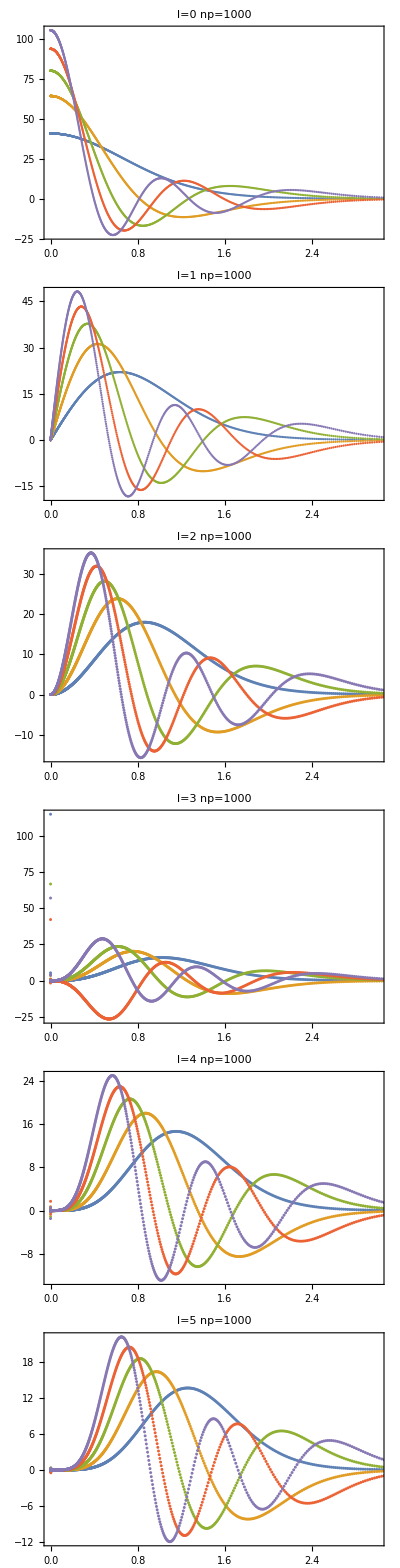

```mathematica
Block[{np=1000,nmax=5,NL=5,lmin=0,lmax=5},Table[ListPlot[Table[Transpose[{pp,psitableLag[l,np,NL][[n]]}],{n,1,nmax}],PlotRange->{{0.,3.},All},ImageSize->Large,Frame->True,PlotLabel->"l="<>ToString[l]<>"  np="<>ToString[np]],{l,lmin,lmax}]//TableForm]
```

### Tables of eigenvalues

```mathematica
TableForm[Table[Join[{ToString[np]},Table[NumberForm[EntableLag[0,np,5][[n]],{16,10}],{n,1,5}]],{np,{50,100,200,400,600,800,1000}}]]
```

50 | 2.3381366586 | 4.0883811896 | 5.5205090235 | 6.7830986753 | 7.9303780220
100 | 2.3381083587 | 4.0879637759 | 5.5205602995 | 6.7865928385 | 7.9436701246
200 | 2.3381074406 | 4.0879499019 | 5.5205598624 | 6.7867044514 | 7.9441187098
400 | 2.3381074114 | 4.0879494586 | 5.5205598293 | 6.7867079757 | 7.9441331176
600 | 2.3381074106 | 4.0879494460 | 5.5205598283 | 6.7867080750 | 7.9441335251
800 | 2.3381074105 | 4.0879494446 | 5.5205598281 | 6.7867080865 | 7.9441335724
1000 | 2.3381074105 | 4.0879494443 | 5.5205598281 | 6.7867080889 | 7.9441335823